# Force on a 3-Level Ba+ Atom with Λ Structure and Optical Driving Fields at 2 Near-Resonant Frequencies

## Compute the force from a typical cooling/repump scheme on a 3-level system as a function of laser parameters and atom properties. Derive the force operator assuming plane wave radiation at 2 frequencies, where each optical field only couples to one near-resonant transition. Find the steady-state density matrix by solving the Optical Bloch Equations, and use the result to compute the expectation value of the force. Apply results to the specific case of Ba+ 1= 6^2 S_(1/2),2= 5^2 D_(3/2),3=6^2 P_(1/2) states, where states1 and |3⟩ are coupled by λ_C = 493.4 nm cooling light and states 2 and |3⟩ are coupled by λ_R = 649.7 nm repump light.

## References

Some of these have in-line citations within this notebook; others are generally useful aids to conceptual understanding.

M. G. Prentiss, N. P. Bigelow, M. S. Shahriar, and P. R. Hemmer, “Forces on three-level atoms including coherent population trapping,” Optics Letters 16, 21 (1991).

M. Lukin and L. Childress, Harvard Physics 285b (AMO II) course notes, (2006).

M. DePalatis, Production of translationally cold barium monohalide ions, Ph.D. Thesis, Georgia Institute of Technology (2013).

C. Foot, Atomic Physics (Oxford University Press, 2005).

H. Metcalf and P. van der Straten, Laser Cooling and Trapping (Springer-Verlag, New York, 1999).

D. Budker, D. F. Kimball, D. P. DeMille, Atomic Physics (Oxford University Press, 2004).

D. N. Stacey, D. M. Lucas, D. T. C. Allcock, D. J. Szwer, and S. C. Webster, “Optical Bloch equations with multiply connected states,” J. Phys. B 41 (2008).

J. P. Gordon and A. Ashkin, “Motion of atoms in a radiation trap,” Phys. Rev. A 21, 1606 (1980).

NIST Atomic Spectra Database Lines Data, Ba II: A. Kramida, Y. Ralchenko, J. Reader, and NIST ASD Team (2015). NIST Atomic Spectra Database (v. 5.3) (Online, accessed Sept. 19, 2017).

G. Janik, W. Nagourney, and H. Dehmelt, “Doppler-free optical spectroscopy on the Ba+ mono-ion oscillator,” J. Opt. Soc. Am. B 2, 8 (1985).

RP Photonics Encyclopedia of Laser Physics and Technology (Online, accessed Oct. 5, 2017)

G. Gopakumar, H. Merlitz, R. K. Chaudhuri, B. P. Das, U. S. Mahapatra, and D. Mukherjee, “Electric dipole and quadrupole transition amplitudes for Ba+ using the relativistic coupled-cluster method,” Phys. Rev. A 66, 032505 (2002).

U. I. Safronova and M. S. Safronova, “Excitation energies, E1, M1, and E2 transition rates, and lifetimes in Ca+, Sr+, Cd+, Ba+ and Hg+,” Canadian Journal of Physics 89 (2011).

## Problem Statement

```mathematica
-Graphics-
We consider a 3-level Λ system as in Ref. [1] with states 1&3 coupled by a single optical field and 2&3 coupled by a different optical field. States 1&2 are assumed uncoupled. The optical fields have the following form:
```

E_C = E_C(r) ϵ_C(r) e^i[ω_C t + ϕ_C(r)]
E_R = E_R(r) ϵ_R(r) e^i[ω_R t + ϕ_R(r)],

where E_C(E_R), ϵ_C (ϵ_R), ω_C (ω_R), and ϕ_C (ϕ_R) are the magnitude, polarization unit vector, angular frequency, and phase of the cooling (repump) field, respectively.  E_C connects only states 1 and 3, while E_R connects only 2 and 3. Generically, the field magnitude, polarization, and phase may vary in space, but we will restrict ourselves to the case of plane waves, where E_L is constant (for L ∈ {C,R}), ϵ_L= z, and ϕ_L= k_L x. The laser linewidths are Γ_C and Γ_R for the cooling and repump lasers, respectively, while the transition partial linewidths (i.e., Einstein A-coefficients) are Γ_1 and Γ_2. The total linewidth of the excited state is assumed to be Γ = Γ_1+Γ_2, i.e., the branching ratios to other states are small (<< 1). The resonant transition frequencies are ω_1 and ω_2, so the average 1-photon detuning δ and the 2-photon detuning Δ are given by:

δ = (δ_C+δ_R)/2=[(ω_C-ω_1)+(ω_R-ω_2)]/2
Δ = δ_C-δ_R= (ω_C-ω_1) - (ω_R-ω_2),

where the individual laser detunings are δ_C=δ+Δ/2 for the cooling laser and δ_R=δ-Δ/2 for the repump.

In this notebook, we will calculate the force exerted this atom by the laser beams. We will largely follow Ref. [1], but since there are huge gaps in the derivations in this reference, we will also pull information from other references and from Eric Hudson’s “Simple 3-level density matrix” Mathematica notebook, which performs a very similar calculation.

## Sketch of Solution

Recall that the expectation value of an operator A is <A> = Tr[ρA] (see, e.g., Ref. [6], Appendix G), where ρ is the density matrix. Recall further that in the Heisenberg picture, the time-dependence of an operator A is given by dA/dt = 1/iℏ [H,A], where H is the Hamiltonian of the system (see, e.g., Ref. [8], near Eq. (4)). When applied to the density matrix, this formula is called the Liouville equation (see, e.g., Ref. [6], Appendix G). Recall finally that the optical Bloch equations give the time-dependence of the density matrix using the Heisenberg formula plus an additional relaxation term L due to non-unitary couplings to a dissipative environment (see, e.g., Ref. [2], Ch. 3 and Ref. [3], Ch. 2.2), such that the form of the OBEs is dρ/dt = [H,ρ]/iℏ + L.

Our approach will therefore be as follows: First, we will write down the Hamiltonian for the three-level system in matrix form, including couplings and energy splittings. We will work in the rotating frame to eliminate time-dependent terms (see e.g. Ref. [2], Ch. 2.1) and use the rotating wave approximation (RWA) to eliminate components of the field that oscillate rapidly (and therefore quickly average to zero) in the rotating frame. This will result in a 3x3 matrix whose diagonal terms are given by the detuning of each level from its respective transition frequency (i.e., its frequency in the appropriate rotating frame), and whose off-diagonal terms are given by the Rabi frequency coupling strengths Ω_j= μ_j·E_j of the two lower states to the excited state 3. The form of this Hamiltonian is: H = -ℏδ 33+ ℏΔ/211-ℏΔ/222-[ℏ/2(Ω_C31+ Ω_R32+ c.c.)].

Next, we will write down the Lindblad relaxation operator L using Eq. (2.40-43) in Ref. [3]. Its form is: L = Σ(2 C_n ρC_n^†-ρC_n^†C_n-C_n^†C_n ρ)/2, where C_n=√Γ_n A_n. Here, A_n are operators associated with system-environment couplings, and Γ_n are the associated relaxation rates.

Putting the Hamiltonian and Lindblad operator results together, we will express the time-dependence of the density matrix in the optical Bloch equation:

dρ/dt = [H,ρ]/i ℏ + L

We will then set the time derivative of ρ equal to zero and use Mathematica to solve this matrix equation for ρ in the steady state. 

Next, we will use Ehrenfest’s theorem, which says that quantum mechanical operators obey classical equations of motion (see e.g. Ref. [5], Ch. 3.1), to compute the force on the atom:

<F> = d<p>/dt = -<∇V> = -<∇H>.

This expression can also be derived from the Hamiltonian formulation of operator time-dependence, recalling that in position space, the momentum operator is -iℏ∇. Since the only spatially dependent parts of the Hamiltonian will turn out to be the couplings due to the optical field, we will find that the force has only off-diagonal terms of the form:

F_j3= (F_(3j))^*=ℏ/2 ∇Ω_j,

where Ω_j= μ_j·E_j, with j = 1 or 2, is the Rabi frequency for each transition. Since the dipole moment operator does not depend explicitly on position, we will just need the gradient of the E-field, which for a uniform plane wave with the definitions given above in the problem statement, is:

∇E_j=i∇ϕ(r)E_j= i k_j E_j.

Using this, we will then be able to express the force as a matrix operator, whose expectation value is given by:

<F> = Tr[ρF],

where we will use the steady-state OBE solution for ρ.

After finding the form of the solution, we will input the numbers for our 137Ba+ system, using atomic constants from the NIST database (Ref. [8]) and experimental laser constants measured by Mike and Prateek. The relevant atomic constants for each transition are the resonant wavelength λ, which gives the transition frequency via ω = 2πc/λ, and the Einstein A coefficient, which is equivalent to the partial linewidth Γ_j. These two constants also give the transition dipole matrix element via the formula (see e.g. Ref. [2], Eq. (2.89)).

μ_j= √(3 ϵ_0 h λ_j^3 Γ_j/16 π^3).

## Setup

```mathematica
SetQuantumAliases[];
ClearAll["Global`*"];
cnj[x_] = Conjugate[x];
hbar = 1.0545718 10^-34;  (*Reduced Planck constant*)
h = 6.62607 10^-34;  (*Planck constant*)
c = 299792458;  (*Speed of light*)
ϵ0 = 8.854 10^-12; (*Vacuum permittivity*)
a0 = 5.29177211 10^-11; (*Bohr radius*)
e = 1.6021766 10^-19; (*elementary charge*)
amu = 1.660539 10^-27;  (*atomic mass unit*)
```

## Find the Density Matrix by Solving the Steady-State OBE

First, let’s write the 3-level density matrix in generic form:

```mathematica
ρform = {{ρ11,ρ12,ρ13},{ρ21,ρ22,ρ23},{ρ31,ρ32,ρ33}};
ρform//MatrixForm
```

(ρ11 | ρ12 | ρ13
ρ21 | ρ22 | ρ23
ρ31 | ρ32 | ρ33)

By examining the diagram in the “Problem Statement” section, we can write down the Hamiltonian for the Λ system as discussed in the “Solution Sketch” section. In the appropriate rotating frame after making the RWA, the Hamiltonian is:
	H = -ℏδ 33+ ℏΔ/211-ℏΔ/222-[ℏ/2(Ω_C31+ Ω_R32+ c.c.)], or in matrix form:

```mathematica
hamiltonian = ℏ/2 {{Δ,0,-cnj[ΩC]},{0,-Δ,-cnj[ΩR]},{-ΩC,-ΩR,-2δ}};
hamiltonian//MatrixForm
```

((Δ ℏ)/2 | 0 | -1/2 ℏ Conjugate[ΩC]
0 | -(Δ ℏ)/2 | -1/2 ℏ Conjugate[ΩR]
-(ΩC ℏ)/2 | -(ΩR ℏ)/2 | -δ ℏ)

Next, we compute the Lindblad operator, following the procedure described in Eq. (2.40-43) in Ref. [3]:
	L = Σ(2 C_n ρC_n^†-ρC_n^†C_n-C_n^†C_n ρ)/2, where
	C_n=√Γ_n A_n.
Here, A_n are operators associated with system-environment couplings, and Γ_n are the associated relaxation rates. In particular, for this system:
	C_1=√Γ_2 23, C_2=√Γ_1 13, C_3= √Γ_C 11, C_4= √Γ_R 22.
After some construction, the Lindblad operator can be represented in matrix form as follows:

```mathematica
lindblad ={{Γ1 ρ33, -(ΓC + ΓR)ρ12/2,-(ΓC + Γ1+Γ2)/2 ρ13},{-(ΓC+ΓR)/2 ρ21,Γ2 ρ33, -(ΓR +Γ1+Γ2)/2 ρ23},{-(ΓC + Γ1 + Γ2)/2 ρ31, -(ΓR+Γ1+Γ2)/2 ρ32,-(Γ1+Γ2) ρ33}};
lindblad//MatrixForm
```

(Γ1 ρ33 | 1/2 (-ΓC-ΓR) ρ12 | 1/2 (-Γ1-Γ2-ΓC) ρ13
1/2 (-ΓC-ΓR) ρ21 | Γ2 ρ33 | 1/2 (-Γ1-Γ2-ΓR) ρ23
1/2 (-Γ1-Γ2-ΓC) ρ31 | 1/2 (-Γ1-Γ2-ΓR) ρ32 | (-Γ1-Γ2) ρ33)

Now we are ready to generate the right-hand side of the OBE (see “Sketch of Solution” section above):

```mathematica
OBEmatrix = FullSimplify[1/(I ℏ) (hamiltonian.ρform - ρform.hamiltonian)+lindblad];
OBEmatrix//MatrixForm
```

(Γ1 ρ33-(ⅈ ρ13 ΩC)/2+1/2 ⅈ ρ31 Conjugate[ΩC] | 1/2 (-(ΓC+ΓR+2 ⅈ Δ) ρ12-ⅈ ρ13 ΩR+ⅈ ρ32 Conjugate[ΩC]) | 1/2 (-(Γ1+Γ2+ΓC+ⅈ (2 δ+Δ)) ρ13-ⅈ (ρ11-ρ33) Conjugate[ΩC]-ⅈ ρ12 Conjugate[ΩR])
1/2 (-(ΓC+ΓR-2 ⅈ Δ) ρ21-ⅈ ρ23 ΩC+ⅈ ρ31 Conjugate[ΩR]) | Γ2 ρ33-(ⅈ ρ23 ΩR)/2+1/2 ⅈ ρ32 Conjugate[ΩR] | 1/2 (-(Γ1+Γ2+ΓR+2 ⅈ δ-ⅈ Δ) ρ23-ⅈ ρ21 Conjugate[ΩC]-ⅈ (ρ22-ρ33) Conjugate[ΩR])
1/2 (-(Γ1+Γ2+ΓC-ⅈ (2 δ+Δ)) ρ31+ⅈ (ρ11 ΩC-ρ33 ΩC+ρ21 ΩR)) | 1/2 (-(Γ1+Γ2+ΓR-2 ⅈ δ+ⅈ Δ) ρ32+ⅈ (ρ12 ΩC+(ρ22-ρ33) ΩR)) | 1/2 (-2 (Γ1+Γ2) ρ33+ⅈ (ρ13 ΩC+ρ23 ΩR)-ⅈ ρ31 Conjugate[ΩC]-ⅈ ρ32 Conjugate[ΩR]))

Next, we solve the OBE in the steady state by setting the left hand side equal to zero. Note that we also enforce a normalization condition on the density matrix such that its trace is 1:

```mathematica
zeros = {{0,0,0},{0,0,0},{0,0,0}};
zeros//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
ρsolve = Solve[OBEmatrix == zeros && ρ11+ ρ22 + ρ33 ==1,{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32,ρ33}]
```

{{ρ11→(ⅈ Γ1 (-ΓC-ΓR-2 ⅈ Δ) ΩR Conjugate[ΩC] Conjugate[ΩR] (-1/16 ΓC ΩC ΩR Conjugate[ΩC] Conjugate[ΩR]-1/16 ΓR ΩC ΩR Conjugate[ΩC] Conjugate[ΩR]) (-(ⅈ (-Γ2-ΓC-ΓR) Conjugate[ΩC])/(2 Γ1 (ΓC+ΓR))+(ⅈ (Γ1 ΓC+Γ2 ΓC+ΓC^2+Γ1 ΓR+Γ2 ΓR+ΓC ΓR-2 ⅈ ΓC δ-2 ⅈ ΓR δ-2 ⅈ Γ1 Δ-2 ⅈ Γ2 Δ-3 ⅈ ΓC Δ-ⅈ ΓR Δ-4 δ Δ-2 Δ^2+ΩR Conjugate[ΩR]))/(2 (ΓC+ΓR) ΩC)))/(16 (1/8 Γ1 (-ΓC-ΓR-2 ⅈ Δ) ΩR Conjugate[ΩR] (1/8 ⅈ (-ΓC-ΓR+2 ⅈ Δ) (-Γ1-Γ2-ΓC+ⅈ (2 δ+Δ)) Conjugate[ΩC]+1/8 ⅈ ΩR Conjugate[ΩC] Conjugate[ΩR]) (-1/8 ⅈ (-Γ1-Γ2-ΓR+2 ⅈ δ-ⅈ Δ) (-ΓC-ΓR-2 ⅈ Δ) Conjugate[ΩC]-1/2 ⅈ Conjugate[ΩC] (1/4 ΩC Conjugate[ΩC]+1/4 ΩR Conjugate[ΩR]))-1/2 ⅈ Conjugate[ΩC] (1/32 Γ2 (-ΓC-ΓR+2 ⅈ Δ) ΩC ΩR Conjugate[ΩC] Conjugate[ΩR] (-1/8 ⅈ (-Γ1-Γ2-ΓR+2 ⅈ δ-ⅈ Δ) (-ΓC-ΓR-2 ⅈ Δ) Conjugate[ΩC]-1/2 ⅈ Conjugate[ΩC] (1/4 ΩC Conjugate[ΩC]+1/4 ΩR Conjugate[ΩR]))+(-1/16 ΓC ΩC ΩR Conjugate[ΩC] Conjugate[ΩR]-1) (1))))+((1) (-1/16 ⅈ 5 (-1/16 ΓC ΩC ΩR Conjugate[ΩC] Conjugate[ΩR]-1/16 4 1) (1)-1))/(-(-1/2 ⅈ 1 ((-1/16 ΓC ΩC ΩR Conjugate[ΩC] Conjugate[ΩR]-1) (1)-1)+Γ1 1) 1+1),7,ρ33→1/1}}
 |  |  |  |

Assign the density matrix result to the variable ρ, then check result to make sure the sum of the probabilities of occupying each state is unity:

```mathematica
ρ = ρform/.ρsolve[[1]];
FullSimplify[Tr[ρ]]
```

1

Good. Let’s put in some approximate numbers to see if everything makes sense:

```mathematica
(*ΩC = 442 10^6;(*s^-1 Rabi frequency of cooling light calculated from laser intensity and dipole transition matrix element*)
ΩR = 177 10^6;(*s^-1 Rabi frequency of repump light calculated from laser intensity and dipole transition matrix element*)
ΓC = 2 π *1 10^6 ; (*s^-1 Approximate cooling laser linewidth estimated from locking linewidth*)
ΓR = 2 π *1 10^6; (*s^-1 Approximate repump laser linewidth estimated from locking linewidth*)
Γ1 =95 10^6; (*s^-1 Partial linewidth/Einstein A coefficient for 6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition from NIST database*)
Γ2 =31 10^6; (*s^-1 Partial linewidth/Einstein A coefficient for 5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition from NIST database*)
δ = -(Γ1+Γ2)/4; (*s^-1 Approximate laser 2-γ detuning estimated from the Doppler cooling limit (see e.g. Ref. [4] near Eq. 9.28)*)
Δ = -(Γ1-Γ2)/2; (*s^-1 Approximate laser 1-γ detuning estimated from the Doppler cooling limit (see e.g. Ref. [4] near Eq. 9.28)*)
ρ//MatrixForm //N
Tr[ρ.ρ] //N (*The trace of the density matrix squared is 1 iff the system is in a pure state; otherwise, it is < 1*)
Clear[ΩC,ΩR,ΓC,ΓR,Γ1,Γ2,δ,Δ]
```

(0.159825-8.67362×10^-18 ⅈ | -0.300412-0.0113449 ⅈ | -0.00916219-0.00837936 ⅈ
-0.300412+0.0113449 ⅈ | 0.801189-3.64292×10^-17 ⅈ | 0.0395069-0.00682807 ⅈ
-0.00916219+0.00837936 ⅈ | 0.0395069+0.00682807 ⅈ | 0.0389861+2.1684×10^-17 ⅈ)

0.853242-3.49521×10^-17 ⅈ

The imaginary parts of the diagonal elements of ρ are evidently the result of a rounding error. It was initially fairly surprising to me that (a) the excited 6 P_(1/2) state population is so small given the ratios of the Rabi frequencies to the decay rates, and (b) that the majority of the population accumulates in the 5 D_(1/2) state given that only 1 in 4 decays take it there, and the Rabi frequency coupling it to the excited state is large compared to the partial linewidth for 6 P_(1/2)→5 D_(1/2) decay. However, my intuitions are probably only relevant to the 2-state system and break down for the Λ system with its coherences and multiple connections between states. Indeed, regarding point (a), the reason the excited state population is small in this case is that these numbers are near the 2-photon resonance (Δ<Γ). Under typical experimental running conditions, the repump laser is blue-detuned so that the 2-photon detuning is substantial in order to avoid such resonant effects.

The trace of ρ^2 can vary from 0 to 1 and gives a measure of the purity of the state, with 1 being a completely pure state and 0 being a completely incoherent mixture. In this case, the state is mostly pure. If the linewidths and/or spontaneous emission rates are increased by enough, the state gets more and more mixed; however, I’ve noticed that the state purity is non-monotonic, at least in the decay rates.

## Find the Steady-State Density Matrix Under Some Simplifying Assumptions

The results from the previous section are almost untractably ugly, so let’s do a simpler version of this calculation under the assumption that the Rabi frequencies are real (so we don’t need to take complex conjugates), and the laser linewidths are infinitely narrow (Γ_C=Γ_R=0):

```mathematica
ρform = {{ρ11,ρ12,ρ13},{ρ21,ρ22,ρ23},{ρ31,ρ32,ρ33}};
ρform//MatrixForm
```

(ρ11 | ρ12 | ρ13
ρ21 | ρ22 | ρ23
ρ31 | ρ32 | ρ33)

```mathematica
hamiltoniansimp = ℏ/2 {{Δ,0,-ΩC},{0,-Δ,-ΩR},{-ΩC,-ΩR,-2δ}};
hamiltoniansimp//MatrixForm
```

((Δ ℏ)/2 | 0 | -(ΩC ℏ)/2
0 | -(Δ ℏ)/2 | -(ΩR ℏ)/2
-(ΩC ℏ)/2 | -(ΩR ℏ)/2 | -δ ℏ)

```mathematica
lindbladsimp = {{Γ1 ρ33, 0,-(Γ1+Γ2)/2 ρ13},{0,Γ2 ρ33, -(Γ1+Γ2)/2 ρ23},{-(Γ1 + Γ2)/2 ρ31, -(Γ1+Γ2)/2 ρ32,-(Γ1+Γ2) ρ33}};
lindbladsimp//MatrixForm
```

(Γ1 ρ33 | 0 | 1/2 (-Γ1-Γ2) ρ13
0 | Γ2 ρ33 | 1/2 (-Γ1-Γ2) ρ23
1/2 (-Γ1-Γ2) ρ31 | 1/2 (-Γ1-Γ2) ρ32 | (-Γ1-Γ2) ρ33)

```mathematica
OBEmatrixsimp =FullSimplify[1/(I ℏ) (hamiltoniansimp.ρform - ρform.hamiltoniansimp)+lindbladsimp];
OBEmatrixsimp//MatrixForm
```

(Γ1 ρ33-1/2 ⅈ (ρ13-ρ31) ΩC | -1/2 ⅈ (2 Δ ρ12-ρ32 ΩC+ρ13 ΩR) | 1/2 (-(Γ1+Γ2+ⅈ (2 δ+Δ)) ρ13-ⅈ (ρ11 ΩC-ρ33 ΩC+ρ12 ΩR))
1/2 ⅈ (2 Δ ρ21-ρ23 ΩC+ρ31 ΩR) | Γ2 ρ33-1/2 ⅈ (ρ23-ρ32) ΩR | 1/2 (-(Γ1+Γ2+2 ⅈ δ-ⅈ Δ) ρ23-ⅈ (ρ21 ΩC+(ρ22-ρ33) ΩR))
1/2 (-Γ1 ρ31-Γ2 ρ31+ⅈ (2 δ ρ31+Δ ρ31+ρ11 ΩC-ρ33 ΩC+ρ21 ΩR)) | 1/2 (-(Γ1+Γ2-2 ⅈ δ+ⅈ Δ) ρ32+ⅈ (ρ12 ΩC+(ρ22-ρ33) ΩR)) | 1/2 (-2 (Γ1+Γ2) ρ33+ⅈ (ρ13 ΩC-ρ31 ΩC+(ρ23-ρ32) ΩR)))

```mathematica
zeros = {{0,0,0},{0,0,0},{0,0,0}};
zeros//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
ρsolvesimp = Solve[OBEmatrixsimp == zeros && ρ11+ ρ22 + ρ33 ==1,{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32,ρ33}]
```

{{ρ11→(ΩR^2 (4 Γ1^3 Δ^2+8 Γ1^2 Γ2 Δ^2+4 Γ1 Γ2^2 Δ^2+16 Γ1 δ^2 Δ^2+16 Γ1 δ Δ^3+4 Γ1 Δ^4+4 Γ1 Δ^2 ΩC^2+Γ2 ΩC^4-8 Γ1 δ Δ ΩR^2-4 Γ1 Δ^2 ΩR^2+Γ1 ΩC^2 ΩR^2+Γ2 ΩC^2 ΩR^2+Γ1 ΩR^4))/(4 Γ1^2 Γ2 Δ^2 ΩC^2+8 Γ1 Γ2^2 Δ^2 ΩC^2+4 Γ2^3 Δ^2 ΩC^2+16 Γ2 δ^2 Δ^2 ΩC^2-16 Γ2 δ Δ^3 ΩC^2+4 Γ2 Δ^4 ΩC^2+8 Γ2 δ Δ ΩC^4-4 Γ2 Δ^2 ΩC^4+Γ2 ΩC^6+4 Γ1^3 Δ^2 ΩR^2+8 Γ1^2 Γ2 Δ^2 ΩR^2+4 Γ1 Γ2^2 Δ^2 ΩR^2+16 Γ1 δ^2 Δ^2 ΩR^2+16 Γ1 δ Δ^3 ΩR^2+4 Γ1 Δ^4 ΩR^2+8 Γ1 Δ^2 ΩC^2 ΩR^2+8 Γ2 Δ^2 ΩC^2 ΩR^2+Γ1 ΩC^4 ΩR^2+2 Γ2 ΩC^4 ΩR^2-8 Γ1 δ Δ ΩR^4-4 Γ1 Δ^2 ΩR^4+2 Γ1 ΩC^2 ΩR^4+Γ2 ΩC^2 ΩR^4+Γ1 ΩR^6),ρ12→-((ΩC ΩR (-2 ⅈ Γ1 Γ2 Δ ΩC^2-2 ⅈ Γ2^2 Δ ΩC^2+4 Γ2 δ Δ ΩC^2-2 Γ2 Δ^2 ΩC^2+Γ2 ΩC^4-2 ⅈ Γ1^2 Δ ΩR^2-2 ⅈ Γ1 Γ2 Δ ΩR^2-4 Γ1 δ Δ ΩR^2-2 Γ1 Δ^2 ΩR^2+Γ1 ΩC^2 ΩR^2+Γ2 ΩC^2 ΩR^2+Γ1 ΩR^4))/(4 Γ1^2 Γ2 Δ^2 ΩC^2+8 Γ1 Γ2^2 Δ^2 ΩC^2+4 Γ2^3 Δ^2 ΩC^2+16 Γ2 δ^2 Δ^2 ΩC^2-16 Γ2 δ Δ^3 ΩC^2+4 Γ2 Δ^4 ΩC^2+8 Γ2 δ Δ ΩC^4-4 Γ2 Δ^2 ΩC^4+Γ2 ΩC^6+4 Γ1^3 Δ^2 ΩR^2+8 Γ1^2 Γ2 Δ^2 ΩR^2+4 Γ1 Γ2^2 Δ^2 ΩR^2+16 Γ1 δ^2 Δ^2 ΩR^2+16 Γ1 δ Δ^3 ΩR^2+4 Γ1 Δ^4 ΩR^2+8 Γ1 Δ^2 ΩC^2 ΩR^2+8 Γ2 Δ^2 ΩC^2 ΩR^2+Γ1 ΩC^4 ΩR^2+2 Γ2 ΩC^4 ΩR^2-8 Γ1 δ Δ ΩR^4-4 Γ1 Δ^2 ΩR^4+2 Γ1 ΩC^2 ΩR^4+Γ2 ΩC^2 ΩR^4+Γ1 ΩR^6)),ρ13→-((2 Δ ΩC ΩR^2 (2 ⅈ Γ1^2 Δ+2 ⅈ Γ1 Γ2 Δ+4 Γ1 δ Δ+2 Γ1 Δ^2-Γ2 ΩC^2-Γ1 ΩR^2))/(4 Γ1^2 Γ2 Δ^2 ΩC^2+8 Γ1 Γ2^2 Δ^2 ΩC^2+4 Γ2^3 Δ^2 ΩC^2+16 Γ2 δ^2 Δ^2 ΩC^2-16 Γ2 δ Δ^3 ΩC^2+4 Γ2 Δ^4 ΩC^2+8 Γ2 δ Δ ΩC^4-4 Γ2 Δ^2 ΩC^4+Γ2 ΩC^6+4 Γ1^3 Δ^2 ΩR^2+8 Γ1^2 Γ2 Δ^2 ΩR^2+4 Γ1 Γ2^2 Δ^2 ΩR^2+16 Γ1 δ^2 Δ^2 ΩR^2+16 Γ1 δ Δ^3 ΩR^2+4 Γ1 Δ^4 ΩR^2+8 Γ1 Δ^2 ΩC^2 ΩR^2+8 Γ2 Δ^2 ΩC^2 ΩR^2+Γ1 ΩC^4 ΩR^2+2 Γ2 ΩC^4 ΩR^2-8 Γ1 δ Δ ΩR^4-4 Γ1 Δ^2 ΩR^4+2 Γ1 ΩC^2 ΩR^4+Γ2 ΩC^2 ΩR^4+Γ1 ΩR^6)),ρ21→-((ΩC (2 ⅈ Γ1 Γ2 Δ ΩC^2 ΩR+2 ⅈ Γ2^2 Δ ΩC^2 ΩR+4 Γ2 δ Δ ΩC^2 ΩR-2 Γ2 Δ^2 ΩC^2 ΩR+Γ2 ΩC^4 ΩR+2 ⅈ Γ1^2 Δ ΩR^3+2 ⅈ Γ1 Γ2 Δ ΩR^3-4 Γ1 δ Δ ΩR^3-2 Γ1 Δ^2 ΩR^3+Γ1 ΩC^2 ΩR^3+Γ2 ΩC^2 ΩR^3+Γ1 ΩR^5))/(4 Γ1^2 Γ2 Δ^2 ΩC^2+8 Γ1 Γ2^2 Δ^2 ΩC^2+4 Γ2^3 Δ^2 ΩC^2+16 Γ2 δ^2 Δ^2 ΩC^2-16 Γ2 δ Δ^3 ΩC^2+4 Γ2 Δ^4 ΩC^2+8 Γ2 δ Δ ΩC^4-4 Γ2 Δ^2 ΩC^4+Γ2 ΩC^6+4 Γ1^3 Δ^2 ΩR^2+8 Γ1^2 Γ2 Δ^2 ΩR^2+4 Γ1 Γ2^2 Δ^2 ΩR^2+16 Γ1 δ^2 Δ^2 ΩR^2+16 Γ1 δ Δ^3 ΩR^2+4 Γ1 Δ^4 ΩR^2+8 Γ1 Δ^2 ΩC^2 ΩR^2+8 Γ2 Δ^2 ΩC^2 ΩR^2+Γ1 ΩC^4 ΩR^2+2 Γ2 ΩC^4 ΩR^2-8 Γ1 δ Δ ΩR^4-4 Γ1 Δ^2 ΩR^4+2 Γ1 ΩC^2 ΩR^4+Γ2 ΩC^2 ΩR^4+Γ1 ΩR^6)),ρ22→-((-4 Γ1^2 Γ2 Δ^2 ΩC^2-8 Γ1 Γ2^2 Δ^2 ΩC^2-4 Γ2^3 Δ^2 ΩC^2-16 Γ2 δ^2 Δ^2 ΩC^2+16 Γ2 δ Δ^3 ΩC^2-4 Γ2 Δ^4 ΩC^2-8 Γ2 δ Δ ΩC^4+4 Γ2 Δ^2 ΩC^4-Γ2 ΩC^6-4 Γ2 Δ^2 ΩC^2 ΩR^2-Γ1 ΩC^4 ΩR^2-Γ2 ΩC^4 ΩR^2-Γ1 ΩC^2 ΩR^4)/(4 Γ1^2 Γ2 Δ^2 ΩC^2+8 Γ1 Γ2^2 Δ^2 ΩC^2+4 Γ2^3 Δ^2 ΩC^2+16 Γ2 δ^2 Δ^2 ΩC^2-16 Γ2 δ Δ^3 ΩC^2+4 Γ2 Δ^4 ΩC^2+8 Γ2 δ Δ ΩC^4-4 Γ2 Δ^2 ΩC^4+Γ2 ΩC^6+4 Γ1^3 Δ^2 ΩR^2+8 Γ1^2 Γ2 Δ^2 ΩR^2+4 Γ1 Γ2^2 Δ^2 ΩR^2+16 Γ1 δ^2 Δ^2 ΩR^2+16 Γ1 δ Δ^3 ΩR^2+4 Γ1 Δ^4 ΩR^2+8 Γ1 Δ^2 ΩC^2 ΩR^2+8 Γ2 Δ^2 ΩC^2 ΩR^2+Γ1 ΩC^4 ΩR^2+2 Γ2 ΩC^4 ΩR^2-8 Γ1 δ Δ ΩR^4-4 Γ1 Δ^2 ΩR^4+2 Γ1 ΩC^2 ΩR^4+Γ2 ΩC^2 ΩR^4+Γ1 ΩR^6)),ρ23→(2 Δ (-2 ⅈ Γ1 Γ2 Δ ΩC^2 ΩR-2 ⅈ Γ2^2 Δ ΩC^2 ΩR-4 Γ2 δ Δ ΩC^2 ΩR+2 Γ2 Δ^2 ΩC^2 ΩR-Γ2 ΩC^4 ΩR-Γ1 ΩC^2 ΩR^3))/(4 Γ1^2 Γ2 Δ^2 ΩC^2+8 Γ1 Γ2^2 Δ^2 ΩC^2+4 Γ2^3 Δ^2 ΩC^2+16 Γ2 δ^2 Δ^2 ΩC^2-16 Γ2 δ Δ^3 ΩC^2+4 Γ2 Δ^4 ΩC^2+8 Γ2 δ Δ ΩC^4-4 Γ2 Δ^2 ΩC^4+Γ2 ΩC^6+4 Γ1^3 Δ^2 ΩR^2+8 Γ1^2 Γ2 Δ^2 ΩR^2+4 Γ1 Γ2^2 Δ^2 ΩR^2+16 Γ1 δ^2 Δ^2 ΩR^2+16 Γ1 δ Δ^3 ΩR^2+4 Γ1 Δ^4 ΩR^2+8 Γ1 Δ^2 ΩC^2 ΩR^2+8 Γ2 Δ^2 ΩC^2 ΩR^2+Γ1 ΩC^4 ΩR^2+2 Γ2 ΩC^4 ΩR^2-8 Γ1 δ Δ ΩR^4-4 Γ1 Δ^2 ΩR^4+2 Γ1 ΩC^2 ΩR^4+Γ2 ΩC^2 ΩR^4+Γ1 ΩR^6),ρ31→-((2 Δ ΩC ΩR^2 (-2 ⅈ Γ1^2 Δ-2 ⅈ Γ1 Γ2 Δ+4 Γ1 δ Δ+2 Γ1 Δ^2-Γ2 ΩC^2-Γ1 ΩR^2))/(4 Γ1^2 Γ2 Δ^2 ΩC^2+8 Γ1 Γ2^2 Δ^2 ΩC^2+4 Γ2^3 Δ^2 ΩC^2+16 Γ2 δ^2 Δ^2 ΩC^2-16 Γ2 δ Δ^3 ΩC^2+4 Γ2 Δ^4 ΩC^2+8 Γ2 δ Δ ΩC^4-4 Γ2 Δ^2 ΩC^4+Γ2 ΩC^6+4 Γ1^3 Δ^2 ΩR^2+8 Γ1^2 Γ2 Δ^2 ΩR^2+4 Γ1 Γ2^2 Δ^2 ΩR^2+16 Γ1 δ^2 Δ^2 ΩR^2+16 Γ1 δ Δ^3 ΩR^2+4 Γ1 Δ^4 ΩR^2+8 Γ1 Δ^2 ΩC^2 ΩR^2+8 Γ2 Δ^2 ΩC^2 ΩR^2+Γ1 ΩC^4 ΩR^2+2 Γ2 ΩC^4 ΩR^2-8 Γ1 δ Δ ΩR^4-4 Γ1 Δ^2 ΩR^4+2 Γ1 ΩC^2 ΩR^4+Γ2 ΩC^2 ΩR^4+Γ1 ΩR^6)),ρ32→(2 Δ ΩR (2 ⅈ Γ1 Γ2 Δ ΩC^2+2 ⅈ Γ2^2 Δ ΩC^2-4 Γ2 δ Δ ΩC^2+2 Γ2 Δ^2 ΩC^2-Γ2 ΩC^4-Γ1 ΩC^2 ΩR^2))/(4 Γ1^2 Γ2 Δ^2 ΩC^2+8 Γ1 Γ2^2 Δ^2 ΩC^2+4 Γ2^3 Δ^2 ΩC^2+16 Γ2 δ^2 Δ^2 ΩC^2-16 Γ2 δ Δ^3 ΩC^2+4 Γ2 Δ^4 ΩC^2+8 Γ2 δ Δ ΩC^4-4 Γ2 Δ^2 ΩC^4+Γ2 ΩC^6+4 Γ1^3 Δ^2 ΩR^2+8 Γ1^2 Γ2 Δ^2 ΩR^2+4 Γ1 Γ2^2 Δ^2 ΩR^2+16 Γ1 δ^2 Δ^2 ΩR^2+16 Γ1 δ Δ^3 ΩR^2+4 Γ1 Δ^4 ΩR^2+8 Γ1 Δ^2 ΩC^2 ΩR^2+8 Γ2 Δ^2 ΩC^2 ΩR^2+Γ1 ΩC^4 ΩR^2+2 Γ2 ΩC^4 ΩR^2-8 Γ1 δ Δ ΩR^4-4 Γ1 Δ^2 ΩR^4+2 Γ1 ΩC^2 ΩR^4+Γ2 ΩC^2 ΩR^4+Γ1 ΩR^6),ρ33→(4 (Γ1+Γ2) Δ^2 ΩC^2 ΩR^2)/(4 Γ1^2 Γ2 Δ^2 ΩC^2+8 Γ1 Γ2^2 Δ^2 ΩC^2+4 Γ2^3 Δ^2 ΩC^2+16 Γ2 δ^2 Δ^2 ΩC^2-16 Γ2 δ Δ^3 ΩC^2+4 Γ2 Δ^4 ΩC^2+8 Γ2 δ Δ ΩC^4-4 Γ2 Δ^2 ΩC^4+Γ2 ΩC^6+4 Γ1^3 Δ^2 ΩR^2+8 Γ1^2 Γ2 Δ^2 ΩR^2+4 Γ1 Γ2^2 Δ^2 ΩR^2+16 Γ1 δ^2 Δ^2 ΩR^2+16 Γ1 δ Δ^3 ΩR^2+4 Γ1 Δ^4 ΩR^2+8 Γ1 Δ^2 ΩC^2 ΩR^2+8 Γ2 Δ^2 ΩC^2 ΩR^2+Γ1 ΩC^4 ΩR^2+2 Γ2 ΩC^4 ΩR^2-8 Γ1 δ Δ ΩR^4-4 Γ1 Δ^2 ΩR^4+2 Γ1 ΩC^2 ΩR^4+Γ2 ΩC^2 ΩR^4+Γ1 ΩR^6)}}

Ah, much better! :D

Let’s try checking this to make sure the sum of the probabilities of ocuppying each state is unity:

```mathematica
ρsimp = FullSimplify[ρform/.ρsolvesimp[[1]]];
ρsimp //MatrixForm
FullSimplify[Tr[ρsimp]]
```

((ΩR^2 (4 Γ1^3 Δ^2+8 Γ1^2 Γ2 Δ^2+Γ2 ΩC^2 (ΩC^2+ΩR^2)+Γ1 (4 Δ^2 (Γ2^2+(2 δ+Δ)^2+ΩC^2)+(-4 Δ (2 δ+Δ)+ΩC^2) ΩR^2+ΩR^4)))/(Γ2 ΩC^2 (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2)-4 Δ (-2 δ+Δ) ΩC^2+ΩC^4)+(4 Γ1 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+8 (Γ1+Γ2) Δ^2 ΩC^2+(Γ1+2 Γ2) ΩC^4) ΩR^2+(-4 Γ1 Δ (2 δ+Δ)+(2 Γ1+Γ2) ΩC^2) ΩR^4+Γ1 ΩR^6) | (Γ2 ΩC^3 (2 Δ (ⅈ (Γ1+Γ2+2 ⅈ δ)+Δ)-ΩC^2) ΩR+ΩC (2 Γ1 Δ (ⅈ Γ1+ⅈ Γ2+2 δ+Δ)-(Γ1+Γ2) ΩC^2) ΩR^3-Γ1 ΩC ΩR^5)/(Γ2 ΩC^2 (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2)-4 Δ (-2 δ+Δ) ΩC^2+ΩC^4)+(4 Γ1 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+8 (Γ1+Γ2) Δ^2 ΩC^2+(Γ1+2 Γ2) ΩC^4) ΩR^2+(-4 Γ1 Δ (2 δ+Δ)+(2 Γ1+Γ2) ΩC^2) ΩR^4+Γ1 ΩR^6) | (2 Δ ΩC ΩR^2 (-2 ⅈ Γ1^2 Δ+Γ2 ΩC^2+Γ1 (-2 ⅈ Γ2 Δ-2 Δ (2 δ+Δ)+ΩR^2)))/(Γ2 ΩC^2 (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2)-4 Δ (-2 δ+Δ) ΩC^2+ΩC^4)+(4 Γ1 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+8 (Γ1+Γ2) Δ^2 ΩC^2+(Γ1+2 Γ2) ΩC^4) ΩR^2+(-4 Γ1 Δ (2 δ+Δ)+(2 Γ1+Γ2) ΩC^2) ΩR^4+Γ1 ΩR^6)
-(Γ2 ΩC^3 (2 (ⅈ Γ1+ⅈ Γ2+2 δ-Δ) Δ+ΩC^2) ΩR+ΩC (2 ⅈ Γ1 Δ (Γ1+Γ2+ⅈ (2 δ+Δ))+(Γ1+Γ2) ΩC^2) ΩR^3+Γ1 ΩC ΩR^5)/(Γ2 ΩC^2 (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2)-4 Δ (-2 δ+Δ) ΩC^2+ΩC^4)+(4 Γ1 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+8 (Γ1+Γ2) Δ^2 ΩC^2+(Γ1+2 Γ2) ΩC^4) ΩR^2+(-4 Γ1 Δ (2 δ+Δ)+(2 Γ1+Γ2) ΩC^2) ΩR^4+Γ1 ΩR^6) | (ΩC^2 (Γ2 (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2)-4 Δ (-2 δ+Δ) ΩC^2+ΩC^4)+(4 Γ2 Δ^2+(Γ1+Γ2) ΩC^2) ΩR^2+Γ1 ΩR^4))/(Γ2 ΩC^2 (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2)-4 Δ (-2 δ+Δ) ΩC^2+ΩC^4)+(4 Γ1 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+8 (Γ1+Γ2) Δ^2 ΩC^2+(Γ1+2 Γ2) ΩC^4) ΩR^2+(-4 Γ1 Δ (2 δ+Δ)+(2 Γ1+Γ2) ΩC^2) ΩR^4+Γ1 ΩR^6) | (2 Δ ΩC^2 ΩR (2 Γ2 Δ (-ⅈ (Γ1+Γ2)-2 δ+Δ)-Γ2 ΩC^2-Γ1 ΩR^2))/(Γ2 ΩC^2 (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2)-4 Δ (-2 δ+Δ) ΩC^2+ΩC^4)+(4 Γ1 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+8 (Γ1+Γ2) Δ^2 ΩC^2+(Γ1+2 Γ2) ΩC^4) ΩR^2+(-4 Γ1 Δ (2 δ+Δ)+(2 Γ1+Γ2) ΩC^2) ΩR^4+Γ1 ΩR^6)
(2 Δ ΩC ΩR^2 (2 ⅈ Γ1^2 Δ+Γ2 ΩC^2+Γ1 (2 ⅈ Γ2 Δ-2 Δ (2 δ+Δ)+ΩR^2)))/(Γ2 ΩC^2 (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2)-4 Δ (-2 δ+Δ) ΩC^2+ΩC^4)+(4 Γ1 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+8 (Γ1+Γ2) Δ^2 ΩC^2+(Γ1+2 Γ2) ΩC^4) ΩR^2+(-4 Γ1 Δ (2 δ+Δ)+(2 Γ1+Γ2) ΩC^2) ΩR^4+Γ1 ΩR^6) | (2 Δ ΩC^2 ΩR (2 Γ2 Δ (ⅈ (Γ1+Γ2+2 ⅈ δ)+Δ)-Γ2 ΩC^2-Γ1 ΩR^2))/(Γ2 ΩC^2 (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2)-4 Δ (-2 δ+Δ) ΩC^2+ΩC^4)+(4 Γ1 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+8 (Γ1+Γ2) Δ^2 ΩC^2+(Γ1+2 Γ2) ΩC^4) ΩR^2+(-4 Γ1 Δ (2 δ+Δ)+(2 Γ1+Γ2) ΩC^2) ΩR^4+Γ1 ΩR^6) | (4 (Γ1+Γ2) Δ^2 ΩC^2 ΩR^2)/(Γ2 ΩC^2 (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2)-4 Δ (-2 δ+Δ) ΩC^2+ΩC^4)+(4 Γ1 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+8 (Γ1+Γ2) Δ^2 ΩC^2+(Γ1+2 Γ2) ΩC^4) ΩR^2+(-4 Γ1 Δ (2 δ+Δ)+(2 Γ1+Γ2) ΩC^2) ΩR^4+Γ1 ΩR^6))

1

Cool. Let’s put in some approximate numbers to see if everything makse sense:

```mathematica
ΩC = 720 10^6;(*s^-1 Rabi frequency of cooling light calculated from laser intensity and dipole transition matrix element*)
ΩR = 460 10^6;(*s^-1 Rabi frequency of repump light calculated from laser intensity and dipole transition matrix element*)
Γ1 =95 10^6; (*s^-1 Partial linewidth/Einstein A coefficient for 6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition from NIST database*)
Γ2 =31 10^6; (*s^-1 Partial linewidth/Einstein A coefficient for 5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition from NIST database*)
δ = -(Γ1+Γ2)/4; (*s^-1 Approximate laser 1-γ detuning estimated from the Doppler cooling limit (see e.g. Ref. [4] near Eq. 9.28)*)
Δ = -(Γ1-Γ2)/2;
ρsimp//MatrixForm //N
Tr[ρsimp.ρsimp] //N (*The trace of the density matrix squared is 1 iff the system is in a pure state; otherwise, it is < 1*)
Clear[ΩC,ΩR,Γ1,Γ2,δ,Δ]
```

(0.28804 | -0.449866-0.00498654 ⅈ | -0.0179141-0.000385552 ⅈ
-0.449866+0.00498654 ⅈ | 0.709038 | 0.028543-0.000196923 ⅈ
-0.0179141+0.000385552 ⅈ | 0.028543+0.000196923 ⅈ | 0.00292208)

0.99279

The diagonals are strictly real this time, which is good. Interestingly, the state is much purer with an infinitely narrow laser linewidth than with linewidths that are just “a little bit smaller” than the other rates in the problem.

## Find the Expectation Value of the Dipole Force Operator

As discussed above in the “Solution Sketch” section, the dipole force operator is: <F> = d<p>/dt = -<∇V> = -<∇H>. From the form of the Hamiltonian in the “Solving the Steady-State OBE” section, we have:
	<F> = -<∇( -ℏδ 33+ ℏΔ/211-ℏΔ/222-[ℏ/2(Ω_C31+ Ω_R32+ c.c.)])>. 
[Note: This seems to be the point where the Prentiss/Bigelow paper (Ref. [1]) loses a factor of 2. They say that <F>= -<∇V>= <∇(μ·E)>, but this last equality omits a factor of 1/2 that is introduced into the Hamiltonian potential term by the RWA.] Since the only spatially dependent terms in this Hamiltonian are the Ω’s (which depend on the optical field), we can reduce this to:
	<F> =ℏ/2<∇Ω_C31+ ∇Ω_R32+ c.c.>.
Recalling that Ω_L= 1/ℏ  μ_L· E_L(r) e^i[ω_L t+ϕ_L(r)], where L∈{R,C}, and noting that the dipole moment μ does not depend explicitly on r, we find (using j to index the Cartesian spatial coordinates):
	(∇Ω_L) j = 1/ℏ μ_L· (∇_j E_L e^i[ω_L t+ϕ_L(r)] + i E_L ∇_j ϕ e^i[ω_L t+ϕ_L(r)]).
If we further assume μ_L || E_L (because μ is an induced dipole - although since there are two optical fields, and they are not necessarily far-red detuned, this assumption may be invalid), we can deduce that ∇(μ_L·E_L) = ∇(μ_L·E_L) = μ_L∇E_L=μ_LE_L(∇E_L/∇E_L). Then we can write:
	(∇Ω_L)  =  (∇E_L/E_L+ i ∇ϕ_L) Ω_L.
So the force is:
	<F> =ℏ/2< (∇E_C/E_C+ i ∇ϕ_C) Ω_C31+ (∇E_R/E_R+i ∇ϕ_R) Ω_R32+ c.c.>.
In Refs. [1,8], the following notation is introduced: ∇E_L/E_L= α_L,  ∇ϕ_L= β_L. In matrix form, we then have:
	F = ℏ/2(0 | 0 | (α_C-iβ_C)Ω_C
0 | 0 | (α_R-iβ_R)Ω_R
(α_C+iβ_C)Ω_C | (α_R+iβ_R)Ω_R | 0).
I think this form of F is quite general, but for our current purposes, we will now specialize to the case of traveling plane waves. As mentioned in the “Solution Sketch” above, in this case, the E-field amplitude is constant, so ∇E_L/E_L= α_L=0. Meanwhile, the spatially dependent part of the phase is given by ϕ_L = k_Lx, so  ∇ϕ_L = β_L= k_L. The Prentiss-Bigelow paper (Ref. [1]) says that this part of the force is associated with spontaneous processes.

We are now ready to write the dipole force operator in matrix form:

```mathematica
force = ℏ I/2{{0,0,- kC cnj[ΩC]},{0,0,- kR cnj[ΩR]},{ kC ΩC,  kR ΩR, 0}};
force//MatrixForm
```

(0 | 0 | -1/2 ⅈ kC ℏ Conjugate[ΩC]
0 | 0 | -1/2 ⅈ kR ℏ Conjugate[ΩR]
1/2 ⅈ kC ΩC ℏ | 1/2 ⅈ kR ΩR ℏ | 0)

We can now bring in the steady-state density matrix result to compute the expectation value of the force operator, using <A> = Tr[ρA]:

```mathematica
F = FullSimplify[Tr[ρ.force]]
```

((kC Γ1+kR Γ2) ΩC ΩR ℏ Conjugate[ΩC] Conjugate[ΩR] ((Γ1+Γ2+ΓC) (ΓC+ΓR) ΩC Conjugate[ΩC]+(Γ1+Γ2+ΓR) ((Γ1+Γ2+ΓC) ((ΓC+ΓR)^2+4 Δ^2)+(ΓC+ΓR) ΩR Conjugate[ΩR])))/(Γ2 (Γ1+Γ2+ΓC) Abs[ΩC]^6+Abs[ΩC]^4 (2 Γ2 (Γ1+Γ2+ΓC) ((Γ1+Γ2+ΓR) (ΓC+ΓR)+4 δ Δ-2 Δ^2)+(Γ1^2+2 Γ2^2+4 Γ2 (ΓC+ΓR)+3 ΓC (ΓC+ΓR)+Γ1 (3 Γ2+4 ΓC+3 ΓR)) ΩR Conjugate[ΩR])+Γ1 (Γ1+Γ2+ΓR) (2 ((Γ1+Γ2+ΓC) (ΓC+ΓR)-2 Δ (2 δ+Δ)) Abs[ΩR]^4+Abs[ΩR]^6+((ΓC+ΓR)^2+4 Δ^2) ((Γ1+Γ2+ΓC)^2+(2 δ+Δ)^2) ΩR Conjugate[ΩR])+ΩC Conjugate[ΩC] (Γ2 (Γ1+Γ2+ΓC) ((ΓC+ΓR)^2+4 Δ^2) ((Γ1+Γ2+ΓR)^2+(-2 δ+Δ)^2)+(2 Γ1^2+(Γ2+ΓR) (Γ2+3 (ΓC+ΓR))+Γ1 (3 Γ2+4 (ΓC+ΓR))) Abs[ΩR]^4+(2 Γ1^3 (ΓC+ΓR)+(ΓC+ΓR) ((Γ2+ΓR) (2 Γ2^2+4 Γ2 (ΓC+ΓR)+3 ΓC (ΓC+ΓR))+8 Γ2 δ^2)-8 Γ2 ΓR δ Δ+2 (4 Γ2^2+6 ΓC ΓR+5 Γ2 (ΓC+ΓR)) Δ^2+2 Γ1^2 ((ΓC+ΓR) (3 (Γ2+ΓC)+2 ΓR)+4 Δ^2)+Γ1 ((ΓC+ΓR) (6 Γ2^2+10 Γ2 (ΓC+ΓR)+(ΓC+ΓR) (4 ΓC+3 ΓR)+8 δ^2)+8 ΓC δ Δ+2 (8 Γ2+5 (ΓC+ΓR)) Δ^2)) ΩR Conjugate[ΩR]))

Let’s put in some approximate numbers. This calculation returns the force (N) and the change in velocity (m/s) for a Ba+ ion subjected to this force for 1 ms:

```mathematica
(*ΩC = 442 10^6;(*s^-1 Rabi frequency of cooling light calculated from laser intensity and dipole transition matrix element*)
ΩR = 177 10^6;(*s^-1 Rabi frequency of repump light calculated from laser intensity and dipole transition matrix element*)
ΓC = 2 π *1 10^6 ; (*s^-1 Approximate cooling laser linewidth estimated from locking linewidth*)
ΓR = 2 π *1 10^6; (*s^-1 Approximate repump laser linewidth estimated from locking linewidth*)
Γ1 =95 10^6; (*s^-1 Partial linewidth/Einstein A coefficient for 6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition from NIST database*)
Γ2 =31 10^6; (*s^-1 Partial linewidth/Einstein A coefficient for 5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition from NIST database*)
δ = -(Γ1+Γ2)/2; (*s^-1 Approximate laser 1-γ detuning estimated from the Doppler cooling limit (see e.g. Ref. [4] near Eq. 9.28)*)
Δ = -(Γ1-Γ2)/2;
λC = 493.4 10^-9; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavelength (blue)*)
λR = 649.7 10^-9;  (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavelength (red)*)
kC = 2 π/λC; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavenumber*)
kR = 2 π/λR; (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavenumber*)
ℏ = hbar;
F//N
F/(138 amu)*.001 //N (*Change in Ba+ velocity over 1 ms [m/s]*)
Clear[ΩC,ΩR,ΓC,ΓR,Γ1,Γ2,δ,Δ,λC,λR,kC,kR,ℏ]
```

7.19032×10^-21

31.3776

## Compare to Hudson and Prentiss/Bigelow Results

Check my result in certain limiting cases by comparing it to similar results calculated by others. Note that neither the P/B calculation nor Eric’s calculation takes into account the nonzero laser linewidth, and the P/B paper further assumes that Γ2=Γ1.

Result of this notebook’s calculation:

```mathematica
forceEPW[δ_,Δ_] =F;
```

Result of Eric’s “Simple 3-level density matrix” notebook calculation (Because of Eric’s different definitions of the 1- and 2-γ detunings, I have made the following substitutions in his formula: Δ -> -Δ and δ -> -(δ+Δ/2); other modifications are a result of reconciling our choice of notation):

```mathematica
forceEH[δ_,Δ_] :=(4 (Γ2+Γ1) (kR Γ2+kC Γ1) Δ^2 ΩR^2 ΩC^2 ℏ)/(Γ1 ΩR^2 (4 ((Γ2+Γ1)^2+4 (-(δ+Δ/2))^2) Δ^2+8 (-(δ+Δ/2)) Δ ΩR^2+ΩR^4)+(4 Γ2 ((Γ2+Γ1)^2+4 (-(δ+Δ/2)+Δ)^2) Δ^2+8 (Γ2+Γ1) Δ^2 ΩR^2+(Γ2+2 Γ1) ΩR^4) ΩC^2+(-8 Γ2 (-(δ+Δ/2)+Δ) Δ+(2 Γ2+Γ1) ΩR^2) ΩC^4+Γ2 ΩC^6)
```

Result of Prentiss-Bigelow paper, divided by 2 per discussion in previous section (Ref. [1], Eq. 3. The commented-out line is Eric’s interpretation of their result, while the other one is mine. I think they agree.):

```mathematica
(*forcePB[δ_,Δ_] :=( (Γ2+Γ1) Δ^2 4 ℏ ΩC^2 ΩR^2)/((√(ΩC^2+ΩR^2))^6+8δ Δ ( (ΩR^4-ΩC^4) +2 Δ^2(ΩC^2-ΩR^2)) + 4 Δ^2((√(ΩC^2+ΩR^2))^2(4 δ^2+(Γ2+Γ1)^2+Δ^2)-(ΩC^4-4 ΩC^2 ΩR^2+ΩR^4))) (kC + kR)*)
forcePB[δ_,Δ_] := 4ℏ Δ^2 (Γ2+Γ1)ΩC^2 ΩR^2(kC+kR)/((ΩR^2+ΩC^2)^3+8 δ Δ((ΩR^4-ΩC^4)+2 Δ^2(ΩC^2-ΩR^2))+4 Δ^2((ΩR^2+ΩC^2)(4 δ^2+(Γ2+Γ1)^2+Δ^2)-(ΩC^4-4 ΩC^2 ΩR^2+ΩR^4)))
```

My derivation of the force using the setup in the Prentiss-Bigelow paper plus some educated guesses about their unstated assumptions. See discussion in the appendix:

```mathematica
forcePBmyderiv[δ_,Δ_] := (4 (kC+kR) (Γ1+Γ2) Δ^2 ΩC^2 ΩR^2 ℏ)/(4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2) ΩC^2-4 Δ (-2 δ+Δ) ΩC^4+ΩC^6+(4 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+16 Δ^2 ΩC^2+3 ΩC^4) ΩR^2+(-4 Δ (2 δ+Δ)+3 ΩC^2) ΩR^4+ΩR^6)
```

Plot the first three results (all except my derivation of the PB result) together using the following numbers. Assume δ = Δ and plot in units of Γ = Γ1+Γ2. (The condition Γ1 = Γ2 is enforced by the premises of the Prentiss-Bigelow paper.) Return the Rabi frequencies and then the plots. Prentiss-Bigelow result is plotted in orange, Eric’s result is in red, and mine is in blue:

500000000

1000000000

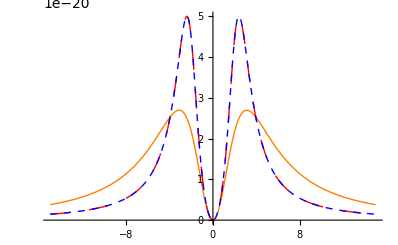

```mathematica
ΓC = 0; (*s^-1 Cooling laser linewidth (inaccurate)*)
ΓR = 0; (*s^-1 Repump laser linewidth (inaccurate)*)
Γ1 =100 10^6; (*s^-1 Partial linewidth/Einstein A coefficient for cooling transition (inaccurate)*)
Γ2 =100 10^6; (*s^-1 Partial linewidth/Einstein A coefficient for repump transition (inaccurate)*)
ΩC = 5 Γ1(*s^-1 Rabi frequency of cooling light (inaccurate)*)
ΩR = 10 Γ2(*s^-1 Rabi frequency of repump light (inaccurate)*)
λC = 493.4 10^-9; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavelength (blue)*)
λR = 649.7 10^-9;  (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavelength (red)*)
kC = 2 π/λC; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavenumber*)
kR = 2 π/λR; (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavenumber*)
ℏ = hbar;
Plot[{forcePB[δ(Γ2+Γ1),δ(Γ2+Γ1)],forceEH[δ(Γ2+Γ1),δ(Γ2+Γ1)],forceEPW[δ(Γ2+Γ1),δ(Γ2+Γ1)]},{δ,-15,15},PlotRange-> All,PlotPoints->500,PlotStyle->{{Thick,Line,Orange},{Thick,Dashing[Large],Red}, {Thick,Dashing[Small],Blue}}]
Clear[ΩC,ΩR,ΓC,ΓR,Γ1,Γ2,δ,Δ,λC,λR,kC,kR,ℏ]
```

These force plots match perfectly as long as ΩC = ΩR; otherwise, the Prentiss-Bigelow result is significantly taller and narrower. All plots show a dip at resonance, characteristic of electromagnetically induced transparency (EIT, see e.g. Ref. [2], Ch. 5.2). I am not sure what the source of the disagreement is; however, in the Appendix below, I try to re-derive their force result using the dressed state basis and guessing at the form of their Lindblad operator. My results differ from those in the P-B paper by a few signs, and I suspect that they are the ones who made a math error somewhere since Mathematica is way better now than it was in 1991, and they probably didn’t even have symbolic manipulation software.

As a check, let’s plot Eric’s result (forceEH), my result (forceEPW), and my derivation of the PB result using their basis (forcePBmyderiv) together using the following numbers. Assume δ = Δ and plot in units of Γ = Γ1+Γ2. (The condition Γ1 = Γ2 is enforced by the premises of the Prentiss-Bigelow paper.) Return the Rabi frequencies and then the plots. My result using the Prentiss-Bigelow setup is plotted in green, Eric’s result is in red, and mine is in blue:

500000000

1000000000

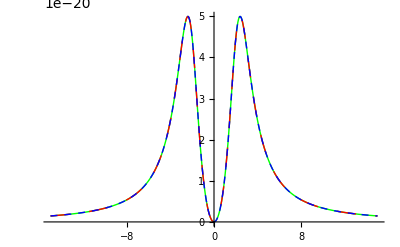

```mathematica
ΓC = 0; (*s^-1 Cooling laser linewidth (inaccurate)*)
ΓR = 0; (*s^-1 Repump laser linewidth (inaccurate)*)
Γ1 =100 10^6; (*s^-1 Partial linewidth/Einstein A coefficient for cooling transition (inaccurate)*)
Γ2 =100 10^6; (*s^-1 Partial linewidth/Einstein A coefficient for repump transition (inaccurate)*)
ΩC = 5 Γ1(*s^-1 Rabi frequency of cooling light (inaccurate)*)
ΩR = 10Γ2(*s^-1 Rabi frequency of repump light (inaccurate)*)
λC = 493.4 10^-9; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavelength (blue)*)
λR = 649.7 10^-9;  (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavelength (red)*)
kC = 2 π/λC; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavenumber*)
kR = 2 π/λR; (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavenumber*)
ℏ = hbar;
Plot[{forcePBmyderiv[δ(Γ2+Γ1),δ(Γ2+Γ1)],forceEH[δ(Γ2+Γ1),δ(Γ2+Γ1)],forceEPW[δ(Γ2+Γ1),δ(Γ2+Γ1)]},{δ,-15,15},PlotRange-> All,PlotPoints->500,PlotStyle->{{Thick,Line,Green},{Thick,Dashing[Large],Red}, {Thick,Dashing[Small],Blue}}]
Clear[ΩC,ΩR,ΓC,ΓR,Γ1,Γ2,δ,Δ,λC,λR,kC,kR,ℏ]
```

OK, since all three results show good agreement now over a variety of parameters, I’m pretty convinced that we’re right, and Prentiss/Bigelow made a math mistake somewhere. Eric agrees that the paper is likely in error and advises using our results, so let’s press on using my formula, “forceEPW.”

Let’s see how we do when the 1- and 2-γ detunings are unequal. Plot all three results together using the following numbers. Assume δ - Δ = nΓ, where n is varied, and plot in units of Γ = Γ1+Γ2. (The condition Γ1 = Γ2 is enforced by the Prentiss-Bigelow result.) Return the partial linewidth, Rabi frequencies, n,  and then the plots. My result using the Prentiss-Bigelow setup is plotted in green, Eric’s result is in red, and mine is in blue:

60000000

720000000

460000000

1/2

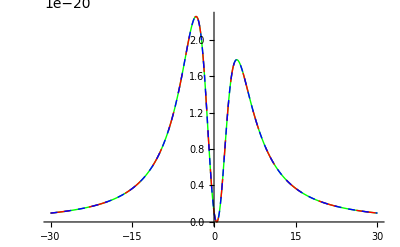

```mathematica
ΓC = 0; (*s^-1 Cooling laser linewidth (inaccurate)*)
ΓR = 0; (*s^-1 Repump laser linewidth (inaccurate)*)
Γ1 =60 10^6; (*s^-1 Partial linewidth/Einstein A coefficient for cooling transition (inaccurate)*)
Γ2 =60 10^6 (*s^-1 Partial linewidth/Einstein A coefficient for repump transition (inaccurate)*)
ΩC = 720 10^6(*s^-1 Rabi frequency of cooling light (inaccurate)*)
ΩR = 460 10^6(*s^-1 Rabi frequency of repump light (inaccurate)*)
λC = 493.4 10^-9; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavelength (blue)*)
λR = 649.7 10^-9;  (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavelength (red)*)
kC = 2 π/λC; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavenumber*)
kR = 2 π/λR; (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavenumber*)
ℏ = hbar;
n = 1/2
Plot[{forcePBmyderiv[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)],forceEH[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)],forceEPW[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)]},{δ,-30,30},PlotRange-> All,PlotPoints->500,PlotStyle->{{Thick,Line,Green},{Thick,Dashing[Large],Red}, {Thick,Dashing[Small],Blue}}]
Clear[ΩC,ΩR,ΓC,ΓR,Γ1,Γ2,δ,Δ,λC,λR,kC,kR,ℏ,n]
```

Agreement between the methods looks good for unequal detuning. Now let’s try comparing Eric’s and my results for the case of unequal partial linewidths. In this case, we do not expect agreement with the PB result (even my version) because unequal branching ratios violates a premise of their paper. Return the partial linewidths, Rabi frequencies, n,  and then the plots. My result using the Prentiss-Bigelow setup is plotted in green, Eric’s result is in red, and mine is in blue:

95000000

31000000

7.2×10^6

460000000

1

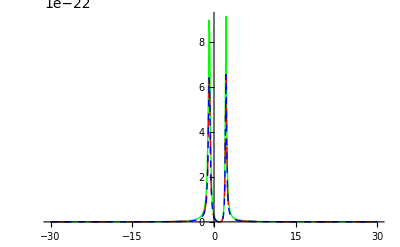

```mathematica
ΓC = 0; (*s^-1 Cooling laser linewidth (inaccurate)*)
ΓR = 0; (*s^-1 Repump laser linewidth (inaccurate)*)
Γ1 =95 10^6 (*s^-1 Partial linewidth/Einstein A coefficient for cooling transition (inaccurate)*)
Γ2 =31 10^6 (*s^-1 Partial linewidth/Einstein A coefficient for repump transition (inaccurate)*)
ΩC = .01*720 10^6(*s^-1 Rabi frequency of cooling light (inaccurate)*)
ΩR = 1*460 10^6(*s^-1 Rabi frequency of repump light (inaccurate)*)
λC = 493.4 10^-9; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavelength (blue)*)
λR = 649.7 10^-9;  (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavelength (red)*)
kC = 2 π/λC; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavenumber*)
kR = 2 π/λR; (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavenumber*)
ℏ = hbar;
n =1
Plot[{forcePBmyderiv[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)],forceEH[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)],forceEPW[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)]},{δ,-30,30},PlotRange-> All,PlotPoints->500,PlotStyle->{{Thick,Line,Green},{Thick,Dashing[Large],Red}, {Thick,Dashing[Small],Blue}}]
Clear[ΩC,ΩR,ΓC,ΓR,Γ1,Γ2,δ,Δ,λC,λR,kC,kR,ℏ,n]
```

Once again, we see good agreement where expected. Now, let’s look at the case where ΓC and ΓR are nonzero. In this case, none of the results should agree since only forceEPW incorporates the laser linewidth decoherence mechanism. The degree of disagreement should be instructive: If they are very different for laser linewidths that are small compared to other rates, that will suggest that my model is inaccurate, and if they are significantly different for realistic linewidths, that will tell us that incorporating laser linewidth effects into the model is important. Return the laser linewidths, partial linewidths, Rabi frequencies, n, and then the plots. My result using the Prentiss-Bigelow setup is plotted in green, Eric’s result is in red, and mine is in blue:

20000000 π

20000000 π

95000000

31000000

720000000

460000000

1

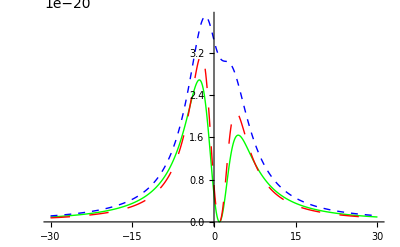

```mathematica
ΓC = 2 π 10 10^6 (*s^-1 Cooling laser linewidth (inaccurate)*)
ΓR = 2 π 10 10^6 (*s^-1 Repump laser linewidth (inaccurate)*)
Γ1 =95 10^6 (*s^-1 Partial linewidth/Einstein A coefficient for cooling transition (inaccurate)*)
Γ2 =31 10^6 (*s^-1 Partial linewidth/Einstein A coefficient for repump transition (inaccurate)*)
ΩC = 1 720 10^6(*s^-1 Rabi frequency of cooling light (inaccurate)*)
ΩR = 1 460 10^6(*s^-1 Rabi frequency of repump light (inaccurate)*)
λC = 493.4 10^-9; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavelength (blue)*)
λR = 649.7 10^-9;  (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavelength (red)*)
kC = 2 π/λC; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavenumber*)
kR = 2 π/λR; (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavenumber*)
ℏ = hbar;
n =1
Plot[{forcePBmyderiv[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)],forceEH[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)],forceEPW[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)]},{δ,-30,30},PlotRange-> All,PlotPoints->500,PlotStyle->{{Thick,Line,Green},{Thick,Dashing[Large],Red}, {Thick,Dashing[Small],Blue}}]
Clear[ΩC,ΩR,ΓC,ΓR,Γ1,Γ2,δ,Δ,λC,λR,kC,kR,ℏ,n]
```

The behavior looks reasonable, and Eric’s and my results are very similar for laser linewidths below 1 MHz (using realistic parameters).

## Compare to Spontaneous Emission Result

If we ignore coherent and stimulated effects, we can assume that the force is due entirely to photon absorption populating the excited state. In steady state, again ignoring stimulated effects, the excitation rate is equivalent to the spontaneous emission rate, so we can estimate the laser force by multiplying the population of the excited state by the decay rate to get the rate of photon absorption, and then multiplying the result by the photon momentum ℏk to get the force (F = Δp/Δt).

```mathematica
(*P33 = FullSimplify[ρ[[3,3]]]
```

(ΩC ΩR Conjugate[ΩC] Conjugate[ΩR] ((Γ1+Γ2+ΓC) (ΓC+ΓR) ΩC Conjugate[ΩC]+(Γ1+Γ2+ΓR) ((Γ1+Γ2+ΓC) ((ΓC+ΓR)^2+4 Δ^2)+(ΓC+ΓR) ΩR Conjugate[ΩR])))/(Γ2 (Γ1+Γ2+ΓC) Abs[ΩC]^6+Abs[ΩC]^4 (2 Γ2 (Γ1+Γ2+ΓC) ((Γ1+Γ2+ΓR) (ΓC+ΓR)+4 δ Δ-2 Δ^2)+(Γ1^2+2 Γ2^2+4 Γ2 (ΓC+ΓR)+3 ΓC (ΓC+ΓR)+Γ1 (3 Γ2+4 ΓC+3 ΓR)) ΩR Conjugate[ΩR])+Γ1 (Γ1+Γ2+ΓR) (2 ((Γ1+Γ2+ΓC) (ΓC+ΓR)-2 Δ (2 δ+Δ)) Abs[ΩR]^4+Abs[ΩR]^6+((ΓC+ΓR)^2+4 Δ^2) ((Γ1+Γ2+ΓC)^2+(2 δ+Δ)^2) ΩR Conjugate[ΩR])+ΩC Conjugate[ΩC] (Γ2 (Γ1+Γ2+ΓC) ((ΓC+ΓR)^2+4 Δ^2) ((Γ1+Γ2+ΓR)^2+(-2 δ+Δ)^2)+(2 Γ1^2+(Γ2+ΓR) (Γ2+3 (ΓC+ΓR))+Γ1 (3 Γ2+4 (ΓC+ΓR))) Abs[ΩR]^4+(2 Γ1^3 (ΓC+ΓR)+(ΓC+ΓR) ((Γ2+ΓR) (2 Γ2^2+4 Γ2 (ΓC+ΓR)+3 ΓC (ΓC+ΓR))+8 Γ2 δ^2)-8 Γ2 ΓR δ Δ+2 (4 Γ2^2+6 ΓC ΓR+5 Γ2 (ΓC+ΓR)) Δ^2+2 Γ1^2 ((ΓC+ΓR) (3 (Γ2+ΓC)+2 ΓR)+4 Δ^2)+Γ1 ((ΓC+ΓR) (6 Γ2^2+10 Γ2 (ΓC+ΓR)+(ΓC+ΓR) (4 ΓC+3 ΓR)+8 δ^2)+8 ΓC δ Δ+2 (8 Γ2+5 (ΓC+ΓR)) Δ^2)) ΩR Conjugate[ΩR]))

```mathematica
(*forcespont[δ_,Δ_] = P33(ℏ kC Γ1 + ℏ kR Γ2);
```

Let’s compare this result with mine and Eric’s. Return the laser linewidths, partial linewidths, Rabi frequencies, n, and then the plots. The spontaneous emission force is plotted in cyan, Eric’s result is in red, and mine is in dark blue; when there is a second plot, it shows the difference between forcespont and forceEPW:

```mathematica
(*ΓC = .1 2 π 10^6 (*s^-1 Cooling laser linewidth (inaccurate)*)
ΓR = .1 2π 10^6 (*s^-1 Repump laser linewidth (inaccurate)*)
Γ1 = 95 10^6 (*s^-1 Partial linewidth/Einstein A coefficient for cooling transition (inaccurate)*)
Γ2 = 31 10^6 (*s^-1 Partial linewidth/Einstein A coefficient for repump transition (inaccurate)*)
ΩC = ΩCfunc[IA1+IA2](*s^-1 Rabi frequency of cooling light (inaccurate)*)
ΩR = ΩRfunc[Ir](*s^-1 Rabi frequency of repump light (inaccurate)*)
λC = 493.4 10^-9; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavelength (blue)*)
λR = 649.7 10^-9;  (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavelength (red)*)
kC = -2 π/λC; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavenumber*)
kR = 2 π/λR; (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavenumber*)
ℏ = hbar;
n =2.1
Plot[{forcespont[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)],forceEH[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)],forceEPW[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)]},{δ,-15,15},PlotRange-> All,PlotPoints->500,PlotStyle->{{Thick,Line,Cyan},{Thick,Dashing[Large],Red}, {Thick,Dashing[Small],Blue}}]
Plot[forcespont[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)]-forceEPW[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)],{δ,-15,15}, PlotRange->All,PlotPoints->500]
δ = (-6.3Γ1+(-14)Γ2)/2; (*s^-1 Laser 2-γ detuning*)
Δ = (-6.3Γ1-(-14) Γ2); (*s^-1 Laser 1-γ detuning*)
P33//N
Clear[ΩC,ΩR,ΓC,ΓR,Γ1,Γ2,δ,Δ,λC,λR,kC,kR,ℏ,n]
```

(Conjugate[ΩCfunc[IA1+IA2]] Conjugate[ΩRfunc[Ir]] ΩCfunc[IA1+IA2] ΩRfunc[Ir] (1.59126×10^14 Conjugate[ΩCfunc[IA1+IA2]] ΩCfunc[IA1+IA2]+1.26628×10^8 (1.37066×10^25+1.25664×10^6 Conjugate[ΩRfunc[Ir]] ΩRfunc[Ir])))/(3.92548×10^15 Abs[ΩCfunc[IA1+IA2]]^6+Abs[ΩCfunc[IA1+IA2]]^4 (2.24326×10^33+2.0358×10^16 Conjugate[ΩRfunc[Ir]] ΩRfunc[Ir])+Conjugate[ΩCfunc[IA1+IA2]] ΩCfunc[IA1+IA2] (3.26946×10^50+2.84622×10^16 Abs[ΩRfunc[Ir]]^4+3.84991×10^33 Conjugate[ΩRfunc[Ir]] ΩRfunc[Ir])+1.20297×10^16 (-7.87308×10^17 Abs[ΩRfunc[Ir]]^4+Abs[ΩRfunc[Ir]]^6+1.56827×10^35 Conjugate[ΩRfunc[Ir]] ΩRfunc[Ir]))

The above results should roughly match the experimental running conditions when the 1-photon detuning in the plot is ~0.9 (Γ1+Γ2): The cooling laser is red-detuned by -Γ1/2 = -7.5 MHz to achieve the Doppler temperature limit, while the repump laser is blue-detuned by +44 MHz in order to maximize the force. Under these running conditions, the excited state population is about 20%, which matches Mike’s estimate.

### A Puzzling Agreement

Evidently my result agrees exactly with the spontaneous emission force result independent of laser parameters. This surprises me: I would have guessed that coherent effects and stimulated forces would become significant near the 2-γ resonance and when the saturation parameters (Rabi frequencies) were sufficiently large, respectively, and that the photon scattering rate approach (<Fspont> = ρ33Γℏk) would neglect them, while my <F> = Tr[ρF] solution would account for them. Let’s try to understand why the two methods are apparently equivalent. 

My force expectation value was found by taking the trace of ρF, where F is the force operator. Here’s what ρF looks like:

```mathematica
MatrixForm[ρform.force]
```

(1/2 ⅈ kC ρ13 ΩC ℏ | 1/2 ⅈ kR ρ13 ΩR ℏ | -1/2 ⅈ kC ρ11 ℏ Conjugate[ΩC]-1/2 ⅈ kR ρ12 ℏ Conjugate[ΩR]
1/2 ⅈ kC ρ23 ΩC ℏ | 1/2 ⅈ kR ρ23 ΩR ℏ | -1/2 ⅈ kC ρ21 ℏ Conjugate[ΩC]-1/2 ⅈ kR ρ22 ℏ Conjugate[ΩR]
1/2 ⅈ kC ρ33 ΩC ℏ | 1/2 ⅈ kR ρ33 ΩR ℏ | -1/2 ⅈ kC ρ31 ℏ Conjugate[ΩC]-1/2 ⅈ kR ρ32 ℏ Conjugate[ΩR])

```mathematica
Tr[ρform.force]
```

1/2 ⅈ kC ρ13 ΩC ℏ+1/2 ⅈ kR ρ23 ΩR ℏ-1/2 ⅈ kC ρ31 ℏ Conjugate[ΩC]-1/2 ⅈ kR ρ32 ℏ Conjugate[ΩR]

Taking the trace of this gives
forceEPW = ℏ i/2 [(ρ13 ΩC - ρ31 ΩC^*)kC + (ρ23 ΩR - ρ32 ΩR^*)kR], while the spontaneous force is 
forcespont = ℏ ρ33( kC Γ1 + kR Γ2).

The equality between the two results implies that (separating the terms proportional to kC and kR)
i/2 (ρj3 Ωj - ρ3j Ωj^*) = ρ33 Γj for j ∈{1,2}, or equivalently,
Im(ρ13 ΩC)/ Γ1 = ρ33 and Im(ρ23 ΩR)/Γ2 = ρ33.

One significant feature: if we examine the Optical Block equations, we see that this implies the condition that element (3,3) of the Lindblad operator term is equal and opposite to element (3,3) of the Hamiltonian commutator term. That is to say, the excitation rate to state 3 and the decay rates from state3 must be equal in steady state. Hence, the original way of calculating the force must have been equivalent to calculating the excitation rate from each state, while the second way is equivalent to calculating the spontaneous decay rate. Still, I was surprised to find this equivalence, as I thought my original force calculation would include stimulated effects, coherences, 2-photon transitions, etc., and not all of these effects contribute to the population of the excited state. 

Perhaps I shouldn’t have been surprised, though, as according to the Prentiss-Bigelow paper (Ref. [1]), if both fields are traveling waves, the only forces are spontaneous. They cite Gordon/Ashkin [8], who have this to say:

I briefly wondered whether the form I chose for the force operator in the “Dipole Force Operator Expectation Value” section implicitly excluded stimulated forces, etc. by assuming that the dipole was always aligned with the applied field, which is untrue in the near-resonant case or the case of multiple optical fields. However, the Gordon/Ashkin paper confirms (near Eq. (17)) that in the case of a single plane wave, at least, the α terms vanish, and the only forces are the spontaneous ones arising from the β terms. Does this mean that coherent effects, stimulated emission, 2-γ transitions, etc. are irrelevant in this system, and I could have simply used a rate model to compute the force? This is also not true, since the force plots above all show a clear dip at Δ = 0 (zero 2-γ detuning), which is characteristic of EIT, a strictly coherent phenomenon.

Eric suggests that the two approaches are equivalent in this case because in the steady state, any coherent process that contributes to the force is canceled out by the reverse process producing an equal and opposite force. For example, a 2-γ transition from state 1 to 2 would produce a momentum kick of ℏ(kC-kR), while a  2-γ transition from state 2 to 1 would produce a momentum kick of ℏ(kR-kC). If these two processes occurred with unequal frequency, then in the absence of any other balancing mechanism, the populations in states 1 and 2 would change, contrary to our steady state assumption. 

We then decided to see what would happen if states 2 and 1 were coupled by spontaneous emission (but no driving optical field). Eric predicted that the two approaches to calculating the force would still be equal in this case because each individual process would still have to obey detailed balance. I thought that if 2 could decay to 1, then 2-γ transitions taking 1 to 2 could proceed faster than those taking 2 to 1, and the population in 2 would still be stabilized by spontaneous emission to 1. Hence, stimulated forces could have a non-zero expectation value, and the F = Tr[ρF] approach would account for these, while the F = ρ33 (Γ_2 ℏ  k_R+ Γ_1 ℏ k_C) + ρ22 (Γ_21 ℏ (k_C- k_R)) approach would miss them. Here’s the calculation and result (Spoiler alert: Eric was right.):

```mathematica
(*lindblad2 ={{Γ1 ρ33+Γ21 ρ22, -(ΓC + ΓR + Γ21)ρ12/2,-(ΓC + Γ1+Γ2)/2 ρ13},{-(ΓC+ΓR + Γ21)/2 ρ21,Γ2 ρ33-Γ21 ρ22, -(ΓR +Γ1+Γ2+ Γ21)/2 ρ23},{-(ΓC + Γ1 + Γ2)/2 ρ31, -(ΓR+Γ1+Γ2 + Γ21)/2 ρ32,-(Γ1+Γ2) ρ33}};
lindblad2//MatrixForm
```

```mathematica
(*OBEmatrix2 = FullSimplify[1/(I ℏ) (hamiltonian.ρform - ρform.hamiltonian)+lindblad2];
OBEmatrix2//MatrixForm
```

```mathematica
(*ρsolve2 = Solve[OBEmatrix2 == zeros && ρ11+ ρ22 + ρ33 ==1,{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32,ρ33}]
```

```mathematica
(*ρ2 = ρform/.ρsolve2[[1]];
(*FullSimplify[Tr[ρ2]]*)
```

```mathematica
(*ρ2
```

```mathematica
(*F2 = Tr[ρ2.force];
```

```mathematica
(*forceEPW2[δ_,Δ_] =F2;
```

```mathematica
(*P332 = ρ2[[3,3]];
```

```mathematica
(*P222 = ρ2[[2,2]];
```

```mathematica
(*forcespont2[δ_,Δ_] = P332(ℏ kC Γ1 + ℏ kR Γ2)+P222(ℏ (kC-kR) Γ21);
```

Let’s compare this result with the Tr[ρF] result. Return the laser linewidths, partial linewidths, Rabi frequencies, n, and then the plots. The spontaneous emission force forcespont2 is plotted in cyan and my calculation from this notebook forceEPW is in dark blue. The second plot shows the difference between forcespont2 and forceEPW, and the outputs below the plots give the 2 forces for particular 1- and 2-γ detunings and the populations of states 2 and 3:

```mathematica
(*ΓC = .1 2 π 10^6 (*s^-1 Cooling laser linewidth (inaccurate)*)
ΓR = .1 2π 10^6 (*s^-1 Repump laser linewidth (inaccurate)*)
Γ1 = 95 10^6 (*s^-1 Partial linewidth/Einstein A coefficient for cooling transition (inaccurate)*)
Γ2 = 31 10^6 (*s^-1 Partial linewidth/Einstein A coefficient for repump transition (inaccurate)*)
Γ21 = 10 10^6 (*s^-1 Partial linewidth/Einstein A coefficient for D->S transition (completely made-up)*)
ΩC = 442 10^6(*s^-1 Rabi frequency of cooling light (inaccurate)*)
ΩR = 177 10^6(*s^-1 Rabi frequency of repump light (inaccurate)*)
λC = 493.4 10^-9; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavelength (blue)*)
λR = 649.7 10^-9;  (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavelength (red)*)
kC = 2 π/λC; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavenumber*)
kR = 2 π/λR; (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavenumber*)
ℏ = hbar;
n =-5
Plot[{forcespont2[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)],forceEPW2[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)]},{δ,-30,30},PlotRange-> All,PlotPoints->500,PlotStyle->{{Thick,Line,Cyan},{Thick,Dashing[Small],Blue}}]
Plot[Re[forcespont2[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)]-forceEPW2[δ(Γ2+Γ1),δ(Γ2+Γ1)-n(Γ2+Γ1)]],{δ,-30,30}, PlotRange->All,PlotPoints->500]
forcespont2[(Γ2+Γ1),(Γ2+Γ1)-n(Γ2+Γ1)]
forceEPW2[(Γ2+Γ1),(Γ2+Γ1)-n(Γ2+Γ1)]
δ = -(Γ1+(-18)Γ2)/4; (*s^-1 Laser 2-γ detuning*)
Δ = -(Γ1-(-18) Γ2)/2; (*s^-1 Laser 1-γ detuning*)
P332//N
P222 //N
Clear[ΩC,ΩR,ΓC,ΓR,Γ1,Γ2,Γ21,δ,Δ,λC,λR,kC,kR,ℏ,n]
```

For a wide variety of cases, these two results are still exactly equal, and I’m back to being confused about why.

## Force vs. Velocity with Realistic Parameters

Let’s try plotting the force in 1-d versus the velocity component along the beamline. At this point, we introduce realistic beam parameters and atomic constants to get accurate numbers.

```mathematica
Clear[ΩC,ΩR,ΓC,ΓR,Γ1,Γ2,δ,Δ,λC,λR,kC,kR,ℏ, κ, Γ, dC, dR, aA1, bA1,aR1,bR1, aA2,bA2,aR2,bR2, ar, br, PA1, PR1, PA2, PR2, Pr, IA1, IA2, IR1, IR2, Ir1,Ir2, δC, δR]
```

```mathematica
ℏ = hbar;
```

Ba+ atomic constants (SI units unless noted)

State 1 corresponds to the ground 6^2 S_(1/2) state, state 2 corresponds to the metastable 5^2 D_(3/2) state, and state 3 corresponds to the excited 6^2 P_(1/2) state.

```mathematica
λC = 493.4 10^-9; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavelength (blue) [m^-1] (Ref. [9])*)
λR = 649.7 10^-9;  (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavelength (red) [m^-1] (Ref. [9])*)
Γ1 = 9.53 10^7;  (*Partial linewidth/Einstein A coefficient for 6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition from NIST database (= 15 MHz) [s^-1] (Ref. [9])*)
Γ2 = 3.10 10^7;  (*Partial linewidth/Einstein A coefficient for 5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition from NIST database (= 5 MHz) [s^-1] (Ref. [9])*)
Γ = Γ1+Γ2; (*Total linewidth of 6^2 Subscript[P, 1/2] state*)
κ = Γ1/Γ2; (*Cooling/repump linewidth ratio*)
kC = 2 π/λC; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavenumber*)
kR = 2 π/λR; (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavenumber*)
dC1 = 3.3380 e a0; (*Reduced dipole matrix element for cooling transition from Safronova & Safronova 2010 (Ref. [12])*)
dR1 = 3.0545 e a0; (*Reduced dipole matrix element for repump transition from Safronova & Safronova 2010 (Ref. [12])*)
dC2 = 3.3266 e a0;(*Dipole matrix element for cooling transition from Gopakumar 2002 (Ref. [13])*)
dR2 = 2.9499 e a0; (*Dipole matrix element for repump transition from Gopakumar 2002 (Ref. [13])*)
dC = Sqrt[(3 ϵ0 h λC^3 Γ1)/(16 π^3)]; (*Transition dipole matrix element for cooling transition calculated as in Lukin AMOI notes Eq. 2.89 (Ref. [2]). Differs by sqrt(2) (smaller) from dB1 and dB2.*)
dR = Sqrt[(3 ϵ0 h λR^3 Γ2)/(16 π^3)]; (*Transition dipole matrix element for repump transition calculated as in Lukin AMOI notes Eq. 2.89 (Ref. [2]). Differs by sqrt(2) (smaller) from dB1 and dB2.*)
(*IsatB = π h c ΓB/(3 λB^3) (*Resonant saturation intensity of cooling transition from Foot (Ref. [4]) Eq. 7.85 - Wrong degeneracy factor for our case, I think*)*)
(*IsatR = π h c ΓR/(3 λR^3) (*Resonant saturation intensity of repump transition from Foot (Ref. [4]) Eq. 7.85 - Wrong degeneracy factor for our case, I think*)*)
IsatC = π/3 h c Γ1/(λC^3);(*Resonant saturation intensity of cooling transition from Foot (Ref. [4]) Eq. 7.85 interpreted in light of DeMille Eq. 3.145 (Ref. [6])*)
IsatR = π/3 h c Γ1/(λR^3); (*Resonant saturation intensity of repump transition from Foot (Ref. [4]) Eq. 7.85 interpreted in light of DeMille Eq. 3.145 (Ref. [6])*)
IsatC1 =(h c/λC) Γ1/(2 λC^2/(2 π) Γ1/Γ); (*Resonant saturation intensity of cooling transition from RP Photonics encyclopedia (Ref. [11]) + Dave's book Eq. 3.145 (Ref. [6])*)
IsatC2 =(h c/λC) Γ2/(2 λC^2/(2 π) Γ1/Γ); (*Resonant saturation intensity of cooling transition from RP Photonics encyclopedia (Ref. [11]) + Dave's book Eq. 3.145 (Ref. [6])*)
IsatR1 =(h c/λR) Γ1/(2 λR^2/(2 π) Γ2/Γ); (*Resonant saturation intensity of cooling transition from RP Photonics encyclopedia (Ref. [11]) + Dave's book Eq. 3.145 (Ref. [6])*)
```

Laser constants (SI units unless noted)

Here is a crude sketch of the Ba+ ion laser cooling setup during a typical ion trap shuttling experiment. Purple lines represent the 493 nm cooling laser beam path, black lines represent the 650 nm repump laser path, the central black blob represents the atomic MOT, and the two ellipses on either side of the MOT represent the ion cloud at its endpoints during the shuttle waveform. The beam size and power numbers listed at the bottom were measured by Teek and Mike on 9/29. The repump laser makes one pass axially (right-to-left in the diagram) through the ion trap, while the cooling beam traces the following path: axial right-to-left, radial at 45 degrees left-to-right, radial retro-reflection at 45 degrees right-to-left, axial retro-reflection left-to-right. The cooling beam expands and loses power on each pass, as indicated by the numbers at the bottom of the diagram.

Since the ion cloud has a typical spatial extent of ~1 mm, we will use the average laser intensities in a 1 mm square centered on each beam to compute the Rabi frequencies. Let’s write the elliptical beam profile in the following form:
I(x,y) = 2 P/(π a b ) Exp[-(2x^2/a^2 + 2y^2/b^2)] , where P is the total power in the beam, I is the intensity profile, and a and b are the beam waists in the x and y directions. By comparing with the formula used in the illustration above, we see that a = w_x and b =  w_y. If we assume that the beam expands linearly in both dimensions, and the flight path length is dominated by the width of the chamber, we obtain the following approximate numbers for the beam waists:

```mathematica
aA1 =((363.459+363.581)/2+370.581)/2 10^-6(*(1.013+(1.200-1.013)/4) 10^-3 *);(*cooling laser x-axis beam waist on 1st axial beam pass in m*)
bA1 =((381.642+378.337)/2+378.337)/2 10^-6(*(0.540+(0.670-0.540)/4) 10^-3*); (*cooling laser y-axis beam waist on 1st axial beam pass in m*)
aR1 =((363.459+363.581)/2+370.581)/2 10^-6(*(1.200-(1.200-1.013)/4) 10^-3 *);(*cooling laser x-axis beam waist on 1st radial beam pass in m*)
bR1 =((381.642+378.337)/2+378.337)/2 10^-6(*(0.670-(0.670-0.540)/4) 10^-3*); (*cooling laser y-axis beam waist on 1st radial beam pass in m*)
aR2 =((363.459+363.581)/2+(568.204+532.291)/2)/2 10^-6(*(1.200+(1.200-1.013)/4) 10^-3 *);(*cooling laser x-axis beam waist on 2nd radial beam pass in m*)
bR2 =((381.642+378.337)/2+(510.631+512.408)/2)/2 10^-6(*(0.670+(0.670-0.540)/4) 10^-3*); (*cooling laser y-axis beam waist on 2nd radial beam pass in m*)
aA2 =((363.459+363.581)/2+(568.204+532.291)/2)/2 10^-6(*(1.013+7/4(1.200-1.013)) 10^-3*);(*cooling laser x-axis beam waist on 2nd axial beam pass in m*)
bA2 =((381.642+378.337)/2+(510.631+512.408)/2)/2 10^-6(*(0.540+7/4(.670-.540)) 10^-3*);(*cooling laser y-axis beam waist on 2nd axial beam pass in m*)

ar1 = ((638.964+592.883)/2+403.974)/2 10^-6(*(2.300) 10^-3 *);(*repump laser x-axis beam waist on single axial beam pass in m*)
br1 = ((619.672+607.873)/2+474.128)/2 10^-6(*(.900) 10^-3*);(*repump laser y-axis beam waist on single axial beam pass in m*)
ar2 = ((638.964+592.883)/2+(866.126+823.464)/2)/2 10^-6(*(2.300) 10^-3 *);(*repump laser x-axis beam waist on single axial beam pass in m*)
br2 = ((619.672+607.873)/2+(941.278+975.921)/2)/2 10^-6(*(.900) 10^-3*);(*repump laser y-axis beam waist on single axial beam pass in m*)
```

Meanwhile, the power on each pass is:

```mathematica
PA1 = (5.322+4.35)/2 10^-3; (*cooling laser power on 1st axial beam pass in W*)
PR1 = 0; (*cooling laser power on 1st radial beam pass in W*)
PR2 = 0; (*cooling laser power on 2nd radial beam pass in W*)
PA2 = (4.35+2.87)/2 10^-3;(*cooling laser power on 2nd axial beam pass in W*)

Pr1 = (2.707+2.22)/2 10^-3; 
(*repump laser power on single axial beam pass in W*)
Pr2= (1.719+2.22)/2 10^-3; 
(*repump laser power on single axial beam pass in W*)
```

As stated above, the spatial profile of the elliptical beam is:

```mathematica
intensity[x_,y_,a_,b_,P_] := 2 P/(π a b) Exp[-(2 x^2/a^2+2 y^2/b^2)]
```

For the axial beam on the first pass, this looks like:

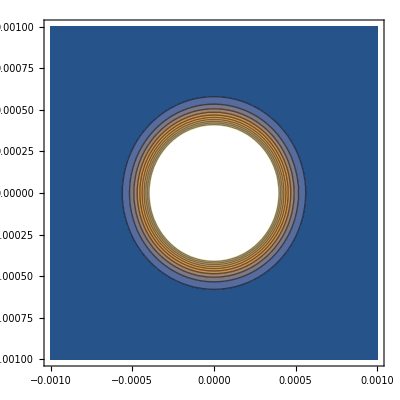

```mathematica
ContourPlot[intensity[x,y,aA1,bA1,PA1],{x,-.001,.001},{y,-.001,.001},Contours->10]
```

The characteristic spatial extent of the ion cloud is 0.5 mm. We now average over the center of each beam to get the peak intensity in W/m^2.

```mathematica
area = (.0005)^2; (*Area in m^2 over which we integrate the beam intensity*)
(*IA1 = NIntegrate[intensity[x,y,aA1,bA1,PA1],{x,-.00025,.00025},{y,-.00025,.00025}]/area;(*cooling laser intensity on 1st axial beam pass in W/m^2*)
IR1 = 0(*NIntegrate[intensity[x,y,aR1,bR1,PR1],{x,-.00025,.00025},{y,-.00025,.00025}]/area*); (*cooling laser intensity on 1st radial beam pass in W/m^2*)
IR2 =0(* NIntegrate[intensity[x,y,aR2,bR2,PR2],{x,-.00025,.00025},{y,-.00025,.00025}]/area*); (*cooling laser intensity on 2nd radial beam pass in W/m^2*)
IA2 = NIntegrate[intensity[x,y,aA2,bA2,PA2],{x,-.00025,.00025},{y,-.00025,.00025}]/area ;(*cooling laser intensity on 2nd axial beam pass in W/m^2*)

Ir1 =  NIntegrate[intensity[x,y,ar1,br1,Pr1],{x,-.00025,.00025},{y,-.00025,.00025}]/area ;(*repump laser intensity on single axial beam pass in W/m^2*)
Ir2 =  NIntegrate[intensity[x,y,ar2,br2,Pr2],{x,-.00025,.00025},{y,-.00025,.00025}]/area ;(*repump laser intensity on single axial beam pass in W/m^2*)
*)
IA1=15519.3;
IA2=12932.7;
Ir1=17435.8;
Ir2=14529.8;
IR1 = 0(*NIntegrate[intensity[x,y,aR1,bR1,PR1],{x,-.00025,.00025},{y,-.00025,.00025}]/area*); (*cooling laser intensity on 1st radial beam pass in W/m^2*)
IR2 =0(* NIntegrate[intensity[x,y,aR2,bR2,PR2],{x,-.00025,.00025},{y,-.00025,.00025}]/area*); (*cooling laser intensity on 2nd radial beam pass in W/m^2*)
```

The Rabi frequencies can then be calculated from the average electric field and the dipole matrix elements:

```mathematica
ΩCfunc[IC_] :=dC Sqrt[2 IC/(c ϵ0)]/ℏ; (*Rabi frequency of cooling light calculated from laser intensity and dipole transition matrix element*)
ΩRfunc[IR_] := dR Sqrt[2 IR/(c ϵ0)]/ℏ; (*Rabi frequency of repump light calculated from laser intensity and dipole transition matrix element*)
```

```mathematica
ΓC = .1 2 π 10^6; (*s^-1 Cooling laser linewidth (estimated based on diode laser specs)*)
ΓR = .1 2 π  10^6; (*s^-1 Repump laser linewidth (estimated based on diode laser specs)*)
```

```mathematica
δC = -28 10^6 2 π;(* -40 10^6 2 π;  -28 10^6 2 π;-72.5 10^6 2 π; -25 10^6 2 π;*)(*s^-1 Detuning of cooling transition (estimated from Doppler cooling limit)*)
δR = -54 10^6 2 π;(* -48 10^6 2 π; -54 10^6 2 π;-81 10^6 2 π; 40 10^6  2 π;*) (*s^-1 Detuning of repump transition (estimated by maximizing force on atoms)*)
```

```mathematica
Clear[ΩC,ΩR,ΓC,ΓR,Γ1,Γ2,δ,Δ,λC,λR,kC,kR,ℏ,n, IR,IC]
```

Now we can calculate the actual forces on the ions as a function of their velocity. At the center of the trap, the ions experience forces in both the x- and y-directions, whereas at the endpoints of the shuttle, the forces are mainly axial. Hence, if we calculate the forces at the center, we can simply turn off the radial forces to get the forces at the endpoints. From the result of this notebook’s force calculation, we have that the force from any pair of co-propagating lasers is:

```mathematica
force1D[δ_,Δ_,ΩC_,ΩR_,kC_,kR_] = F;
```

If the projection of the velocity along the direction of propagation of the cooling laser beam is vp, then we can write the force due to each of the four cooling laser beams as follows:

```mathematica
forceA1[vp_] := force1D[(δC-vp/λC+δR-vp/λR)/2,(δC-δR-(vp/λC-vp/λR)),ΩCfunc[IA1],ΩRfunc[Ir1],kC,kR] (*force due to lasers on 1st cooling laser axial beam pass in N*)
forceA2[vp_]:=force1D[(δC-vp/λC+δR+vp/λR)/2,(δC-δR-(vp/λC+vp/λR)),ΩCfunc[IA2],ΩRfunc[Ir2],kC,-kR] (*force due to lasers on 2nd cooling laser axial beam pass in N*)
forceR1[vp_]:=force1D[(δC-vp/λC+δR+vp/(λR Sqrt[2]))/2,(δC-δR-(vp/λC+vp/(λR Sqrt[2]))),ΩCfunc[IR1],ΩRfunc[Ir1],kC,-kR/(Sqrt[2])] (*force due to lasers on 1st cooling laser radial beam pass in N*)
forceR2[vp_]:=force1D[(δC-vp/λC+δR-vp/(λR Sqrt[2]))/2,(δC-δR-(vp/λC-vp/(λR Sqrt[2]))),ΩCfunc[IR2],ΩRfunc[Ir2],kC,kR/(Sqrt[2])] (*force due to lasers on 1st cooling laser radial beam pass in N*)
```

```mathematica
forceA1det[vp_,δC_,δR_,ΩC_,ΩR_] := force1D[(δC-vp/λC+δR-vp/λR)/2,(δC-δR-(vp/λC-vp/λR)),ΩC,ΩR,kC,kR] (*force due to lasers on 1st cooling laser axial beam pass in N*)
forceA2det[vp_,δC_,δR_,ΩC_,ΩR_]:=force1D[(δC-vp/λC+δR+vp/λR)/2,(δC-δR-(vp/λC+vp/λR)),ΩC,ΩR,kC,-kR] (*force due to lasers on 2nd cooling laser axial beam pass in N*)
forceR1det[vp_,δC_,δR_,ΩC_,ΩR_]:=force1D[(δC-vp/λC+δR+vp/(λR Sqrt[2]))/2,(δC-δR-(vp/λC+vp/(λR Sqrt[2]))),ΩC,ΩR,kC,-kR/(Sqrt[2])] (*force due to lasers on 1st cooling laser radial beam pass in N*)
forceR2det[vp_,δC_,δR_,ΩC_,ΩR_]:=force1D[(δC-vp/λC+δR-vp/(λR Sqrt[2]))/2,(δC-δR-(vp/λC-vp/(λR Sqrt[2]))),ΩC,ΩR,kC,kR/(Sqrt[2])] (*force due to lasers on 1st cooling laser radial beam pass in N*)
```

Forces from each cooling beam pass, treated independently. The force (N) is plotted as a function of the velocity projection (m/s) along the direction of propagation of the cooling laser beam. Blue = 1st axial pass, yellow = 2nd axial pass, green = 1st radial pass, orange = 2nd radial pass.

```mathematica
Plot[{forceA1[vp],forceA2[vp],forceR1[vp],forceR2[vp]},{vp,-1000,1000},PlotRange->All,PlotPoints->1000,AxesLabel->{"Velocity Along Laser (m/s)","Force Along Laser (N)"}]
```

Sum of the forces from the axial cooling beams, treated independently. The force (N) is plotted as a function of the velocity projection (m/s) along the direction of propagation of the 1st axial pass of the cooling laser beam.

```mathematica
δC = -100 10^6 2 π;
δR = -60 10^6 2 π;
δ = (δC+δR)/2;
Δ = δC-δR;
ΩC = ΩCfunc[IA1+IA2]
ΩR = ΩRfunc[Ir1+Ir2]
P33//N
```

8.84777×10^8

8.08209×10^8

P33

```mathematica
7.202698601614358*^8/(2 π)
```

1.14635×10^8

```mathematica
2.6411848839158306*^8/(2 π)
```

4.20358×10^7

```mathematica
Manipulate[Plot[{forceA1det[vp,δC 10^6 2 π,δR 10^6 2 π,ΩCfunc[IA1],ΩRfunc[Ir1]]-forceA2det[-vp,δC 10^6 2 π,δR 10^6 2 π,ΩCfunc[IA2],ΩRfunc[Ir2]]},{vp,-500,500},PlotRange->All,PlotPoints->400,AxesLabel->{"v||A1 (m/s)","Force along A1 (N)"}],{δC,-150,150},{δR,-150,150}]
```

```mathematica
ΩCfunc[IA1]/(10^6 2 π)
ΩCfunc[IA2]/(10^6 2 π)
ΩRfunc[Ir1]/(10^6 2 π)
ΩRfunc[Ir2]/(10^6 2 π)
```

104.

94.9385

95.

86.7226

Plot cooling power vs. velocity. Vary detunings and Rabi frequencies.

```mathematica
Manipulate[Plot[{vp forceA1det[vp,δC 10^6 2 π,δR 10^6 2 π,ΩC 10^6 2 π,ΩR 10^6 2 π]-vp forceA2det[-vp,δC 10^6 2 π,δR 10^6 2 π,ΩC 10^6 2 π/1.2,ΩR 10^6 2 π/1.2]},{vp,-500,500},PlotRange->{-500 10^-20,500 10^-20},PlotPoints->400,AxesLabel->{"v||A1 (m/s)","Power along A1 (N)"}],{δC,-120,100},{δR,-120,100},{ΩC,5,500},{ΩR,5,500}]
```

Plot axial cooling force vs. velocity. Vary detunings and Rabi frequencies.

```mathematica
Manipulate[Plot[{forceA1det[vp,δC 10^6 2 π,δR 10^6 2 π,ΩC 10^6 2 π,ΩR 10^6 2 π]-forceA2det[-vp,δC 10^6 2 π,δR 10^6 2 π,ΩC 10^6 2 π/1.2,ΩR 10^6 2 π/1.2]},{vp,-1000,1000},PlotRange->{-4 10^-20,4 10^-20},PlotPoints->400,AxesLabel->{"v||A1 (m/s)","Force along A1 (N)"}],{δC,-120,100},{δR,-120,100},{ΩC,5,500},{ΩR,5,500}]
```

```mathematica
Clear[δC,δR]
```

Plot axial cooling force vs. velocity.

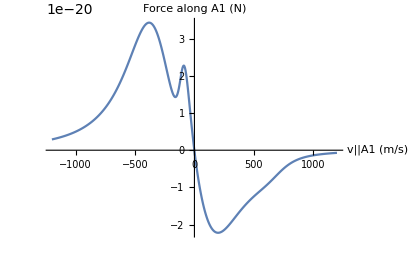

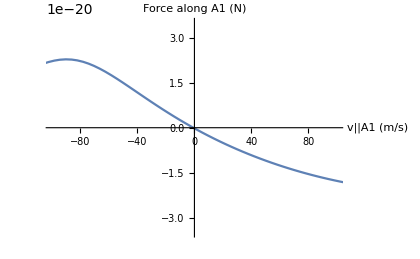

```mathematica
δC = -70.2 10^6 2 π;
δR = -117 10^6 2 π;
δC/(2 π);
δR/(2 π);
Plot[{forceA1[vp]-forceA2[-vp]},{vp,-1200,1200},PlotRange->All,PlotPoints->500,AxesLabel->{"v||A1 (m/s)","Force along A1 (N)"}]
Plot[{force1D[(δC-vp/λC+δR-vp/λR)/2,(δC-δR-(vp/λC-vp/λR)),ΩCfunc[IA1],ΩRfunc[Ir1],kC,kR] -force1D[(δC+vp/λC+δR-vp/λR)/2,(δC-δR-(-vp/λC-vp/λR)),ΩCfunc[IA2],ΩRfunc[Ir2],kC,-kR]},{vp,-1000,1000},PlotRange->{{-100,100},{-3.5 10^-20, 3.5 10^-20}},PlotPoints->500,AxesLabel->{"v||A1 (m/s)","Force along A1 (N)"}]
```

Derivative of the force at v = 0. This gives the linear damping coefficient -α, defined by F = -α v. The units are kg/s. The subsequent line converts the damping coefficient into SIMION units by multiplying by Avogadro’s number x 1000 to get the mass in amu (6.022e23 amu/g*1000g/kg) and converting the time to μs (10^6μs/s). This gives a damping coefficient comparable to the one calculated in the notebook “Ba+_laser_cooling.nb” using Foot Eq. (9.17) (Ref. [4]) and incorporating the effects of laser saturation. In earlier simulations, I used a damping coefficient of γ=0.1/μs, or for 137 Ba, α = γm = 13.7 amu/us.

```mathematica
fderiv = forceA1'[0]+forceA2'[0]
```

-4.1662×10^-22

```mathematica
α = fderiv*(-6.022 10^26)/10^6
```

0.250889

```mathematica
γ = α/137
```

0.0018313

Make a force lookup table in SIMION units for velocity intervals of 0.5 m/s between -500 and +500 m/s

```mathematica
axforcevplookup = Table[(forceA1[vp]-forceA2[-vp])6.022 10^26/(10^9),{vp,-500,500,0.05}];
```

```mathematica
Export["axforcevplookup4.txt",axforcevplookup,"List"]
```

axforcevplookup4.txt

```mathematica
Dimensions[axforcevplookup]
```

{20001}

```mathematica
forcedervplookup=Table[(forceA1'[vp]-forceA2'[-vp])6.022 10^26/(10^12),{vp,-500,500,0.05}];
Export["forcedervplookup4.txt",forcedervplookup,"List"]
```

forcedervplookup4.txt

Sum of the forces from the radial cooling beams, treated independently. The force (N) is plotted as a function of the velocity projection (m/s) along the direction of propagation of the 1st radial pass of the cooling laser beam.

-7.25×10^7

-81000000

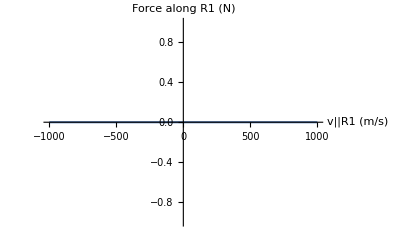

```mathematica
δC/(2 π)
δR/(2 π)
Plot[{forceR1[vp]-forceR2[-vp]},{vp,-1000,1000},PlotRange->All,PlotPoints->500, AxesLabel->{"v||R1 (m/s)","Force along R1 (N)"}]
```

Generate force lookup tables for

```mathematica
vplookup = Table[vp,{vp,-500,500,0.05}];
radforcevplookup = Table[(forceR1[vp]-forceR2[-vp])6.022 10^26/(10^9),{vp,-500,500,0.05}];
```

```mathematica
Export["vplookupfine.txt",vplookup,"List"]
```

vplookupfine.txt

```mathematica
Export["radforcevplookuppeakfine_-100_-60.txt",radforcevplookup,"List"]
```

radforcevplookuppeakfine_-100_-60.txt

```mathematica
Dimensions[radforcevplookup]
```

{2001}

```mathematica
Clear[δC,δR]
```

Plot the normalized axial force derivative F’(v=0)/|F(v=0)|  as a function of the cooling and repump detunings:

```mathematica
forcegradscan = Table[Table[{δC/(2 π),δR/(2 π),(forceA1'[0]+forceA2'[0])/Abs[forceA1[0]-forceA2[0]]},{δC,-150 10^6 2 π,150 10^6 2 π, 2 π 10^6}],{δR,-150 10^6 2 π,150 10^6 2 π, 2 π 10^6}];
```

```mathematica
forcegradzeroscan = Table[Table[{δC/(2 π),δR/(2 π),(forceA1'[0]+forceA2'[0])},{δC,-150 10^6 2 π,150 10^6 2 π, 3 π 10^6}],{δR,-150 10^6 2 π,150 10^6 2 π, 3 π 10^6}];
```

```mathematica
ListPlot3D[Flatten[forcegradscan,1], PlotRange->{-1,1.},AxesLabel->{"δC (MHz)","δR (MHz)","F'[v=0]/|F[v=0]|"}]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[forcegradzeroscan,1],PlotRange->{-1.5 10^-21,-.04 10^-21},AxesLabel->{"δC (MHz)","δR (MHz)","F'[v=0]"},ViewPoint->Front]
```

-Graphics3D-

-Graphics3D-

```mathematica
ListContourPlot[Flatten[forcegradscan,1],Contours->100,FrameLabel->{"δC (MHz)", "δR (MHz)"},PlotRange->{-.4,.4},ColorFunction->"GreenPinkTones",ContourStyle->None]
```

```mathematica
forcegradscan2 = Table[Table[{δC/(2 π),δR/(2 π),(forceA1'[0]+forceA2'[0])/Abs[forceA1[0]-forceA2[0]]},{δC,-50 10^6 2 π,50 10^6 2 π, π 10^6}],{δR,-50 10^6 2 π,50 10^6 2 π,  π 10^6}];
```

```mathematica
ListContourPlot[Flatten[forcegradscan2,1],Contours->80,FrameLabel->{"δC (MHz)", "δR (MHz)"},ColorFunction->"GreenPinkTones"]
```

-Graphics-

```mathematica
forcegradscan2
```

{{{-50000000,-50000000,1.74466},{-49500000,-50000000,-1.49242},{-49000000,-50000000,-32.4022},{-48500000,-50000000,-3.07436},{-48000000,-50000000,-1.59197},{-47500000,-50000000,-1.10252},{-47000000,-50000000,-0.855588},{-46500000,-50000000,-0.706852},185,{46500000,-50000000,0.00784587},{47000000,-50000000,0.00774929},{47500000,-50000000,0.00765547},{48000000,-50000000,0.00756432},{48500000,-50000000,0.00747576},{49000000,-50000000,0.00738973},{49500000,-50000000,0.00730615},{50000000,-50000000,0.00722496}},200}
 |  |  |  |

### Excited State Population vs. Detuning

In practice, the laser detunings are optimized by maximizing the ion fluorescence. Here we plot the 6^2 P_(1/2) steady-state population as a function of the cooling and repump laser detunings for just the first axial beam pass.

```mathematica
ρ33func[δ_,Δ_] = P33;
```

```mathematica
ℏ = hbar;
ΓC = .1 2 π 10^6; (*s^-1 Cooling laser linewidth*)
ΓR = .1 2π 10^6; (*s^-1 Repump laser linewidth*)
Γ1 = 95 10^6; (*s^-1 Partial linewidth/Einstein A coefficient for cooling transition*)
Γ2 = 31 10^6; (*s^-1 Partial linewidth/Einstein A coefficient for repump transition*)
ΩC = ΩCfunc[IA1];(*s^-1 Rabi frequency of cooling light*)
ΩR = ΩRfunc[Ir];(*s^-1 Rabi frequency of repump light*)
λC = 493.4 10^-9; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavelength (blue)*)
λR = 649.7 10^-9;  (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavelength (red)*)
kC = 2 π/λC; (*6^2 Subscript[S, 1/2]->6^2 Subscript[P, 1/2] cooling transition wavenumber*)
kR = 2 π/λR; (*5^2 Subscript[D, 3/2]->6^2 Subscript[P, 1/2] repump transition wavenumber*)
detuningscan = Table[Table[{i,j,ρ33func[2 π(δCvar+δRvar)/2,2 π (δCvar-δRvar)]/.{δCvar->i,δRvar->j}},{i,-150 10^6,150 10^6,2 10^6}],{j,-150 10^6,150 10^6,2 10^6}];
ρ33func[2 π(-25+40) 10^6/2,2 π(-25-40) 10^6]
ρ33func[2 π(-40+25) 10^6/2,2 π(-40-25) 10^6]
Clear[ΩC,ΩR,ΓC,ΓR,Γ1,Γ2,δ,Δ,λC,λR,kC,kR,ℏ]
```

0.308759

0.274033

```mathematica
115/88.
```

1.30682

Excited state population vs. cooling laser detuning (MHz, x-axis) and repump detuning (MHz, y-axis).

```mathematica
ListContourPlot[Flatten[detuningscan,1],PlotRange->{0.05,0.2},FrameLabel->{"δC (MHz)", "δR (MHz)"},Contours->40,ContourStyle->None]
```

-Graphics-

```mathematica
ListPlot3D[Flatten[detuningscan,1],PlotRange->All,AxesLabel->{"δC (MHz)", "δR (MHz)","ρ33"}]
```

-Graphics3D-

The contour plot above suggests that δC = -25 MHz and δR = 40 MHz may be typical detuning parameters used in the experiment; however, as Eric points out, fluorescence will not be maximized if the cooling under these conditions is terrible: in this case, ions will be heated out of the laser beam path and will stop fluorescing. Therefore, optimizing the cooling force might be a better proxy for the experimental optimization routine. Unfortunately, it looks like we’ll have to run the simulation with a few different detunings.

### Transient Force Calculation

In a further effort to understand the steady-state equivalence between the two force calculations F = Tr[ρF] and  F = ρ33 (Γ_2 ℏ  k_R+ Γ_1 ℏ k_C) + ρ22 (Γ_21 ℏ (k_C- k_R)), let’s examine the force in the transient case by numerically re-solving the time-dependent OBE and re-computing the force according to the two methods. We will assume that all the population is initially in state 1.

```mathematica
ρt[t_] = {{ρ11[t],ρ12[t],ρ13[t]},{ρ21[t],ρ22[t],ρ23[t]},{ρ31[t],ρ32[t],ρ33[t]}};
```

```mathematica
OBEmatrixt[t_] = {{Γ1 ρ33[t]-(ⅈ ρ13[t] ΩC)/2+1/2 ⅈ ρ31[t] Conjugate[ΩC],1/2 (-(ΓC+ΓR+2 ⅈ Δ) ρ12[t]-ⅈ ρ13[t] ΩR+ⅈ ρ32[t] Conjugate[ΩC]),1/2 (-(Γ1+Γ2+ΓC+ⅈ (2 δ+Δ)) ρ13[t]-ⅈ (ρ11[t]-ρ33[t]) Conjugate[ΩC]-ⅈ ρ12[t] Conjugate[ΩR])},{1/2 (-(ΓC+ΓR-2 ⅈ Δ) ρ21[t]-ⅈ ρ23[t] ΩC+ⅈ ρ31[t] Conjugate[ΩR]),Γ2 ρ33[t]-(ⅈ ρ23[t] ΩR)/2+1/2 ⅈ ρ32[t] Conjugate[ΩR],1/2 (-(Γ1+Γ2+ΓR+2 ⅈ δ-ⅈ Δ) ρ23[t]-ⅈ ρ21[t] Conjugate[ΩC]-ⅈ (ρ22[t]-ρ33[t]) Conjugate[ΩR])},{1/2 (-(Γ1+Γ2+ΓC-ⅈ (2 δ+Δ)) ρ31[t]+ⅈ (ρ11[t] ΩC-ρ33[t] ΩC+ρ21[t] ΩR)),1/2 (-(Γ1+Γ2+ΓR-2 ⅈ δ+ⅈ Δ) ρ32[t]+ⅈ (ρ12[t] ΩC+(ρ22[t]-ρ33[t]) ΩR)),1/2 (-2 (Γ1+Γ2) ρ33[t]+ⅈ (ρ13[t] ΩC+ρ23[t] ΩR)-ⅈ ρ31[t] Conjugate[ΩC]-ⅈ ρ32[t] Conjugate[ΩR])}};
```

```mathematica
ΩC = ΩCfunc[IA1];(*s^-1 Rabi frequency of cooling light*)
ΩR = ΩRfunc[Ir];(*s^-1 Rabi frequency of repump light*)
δ = (δC+δR)/2;
Δ = (δC-δR);
```

```mathematica
ρtransient= NDSolve[OBEmatrixt[t] ==  ρt'[t] && ρ11[0]==1 && ρ12[0]==0 && ρ13[0]==0&& ρ21[0]==0 && ρ22[0]==0 && ρ23[0]==0 && ρ31[0]==0 && ρ32[0]==0 && ρ33[0]==0,{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32,ρ33},{t,0,.00001},AccuracyGoal->25,PrecisionGoal->25,WorkingPrecision->35];
```

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (35.).

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 8.1814675299416377315269113096593523×10^-7.

```mathematica
ρtsolve[t_] = ρt[t]/.ρtransient;
```

Plot the evolution of the Λ system populations as they settle to the steady state. Blue = 1, Yellow = 2, Green = 3. The Rabi frequency is ~100 MHz, so the ~10 ns periodicity associated with the wiggles makes sense. The initial condition ρ11 = 1, ρ22 = ρ33 = 0 is satisfied, and the steady-state populations look fairly realistic.

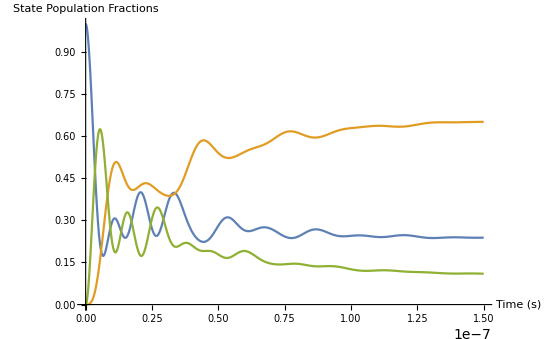

```mathematica
Plot[{Evaluate[ρ11[t]/.ρtransient],Evaluate[ρ22[t]/.ρtransient],Evaluate[ρ33[t]/.ρtransient]},{t,0,.00000015}, PlotRange->All,AxesLabel->{"Time (s)","State Population Fractions"}]
```

Plot the force as a function of time using the two methods. The spontaneous emission force is plotted in cyan and the total force is in dark blue. At last, we find the expected disagreement!

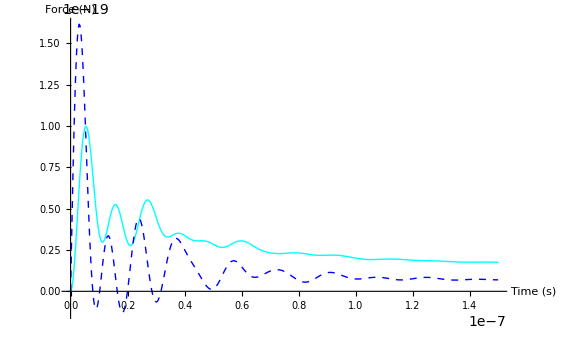

```mathematica
Plot[{Evaluate[ρ33[t]/.ρtransient]*(ℏ kC Γ1 + ℏ kR Γ2),Re[Tr[Evaluate[ρtsolve[t]].force]]},{t,0,.00000015},PlotPoints->500, PlotRange->All,PlotStyle->{{Thick,Line,Cyan},{Thick,Dashing[Small],Blue}},AxesLabel->{"Time (s)","Force (N)"}]
```

## Appendix: Attempt to Derive Force Equation from Prentiss-Bigelow Paper (Ref. [1])

The form of the Hamiltonian in the dressed state basis is given in the P-B paper as:

```mathematica
hamiltonianTDPB = ℏ/(2 (ΩC^2+ΩR^2))*{{Δ (ΩR^2-ΩC^2), 2Δ ΩC ΩR,0},{2Δ ΩC ΩR,-Δ (ΩR^2-ΩC^2),-Sqrt[(ΩC^2+ΩR^2)]^3},{0,-Sqrt[(ΩC^2+ΩR^2)]^3,-2δ(ΩC^2+ΩR^2)}};
hamiltonianTDPB//MatrixForm
```

((Δ (-ΩC^2+ΩR^2) ℏ)/(2 (ΩC^2+ΩR^2)) | (Δ ΩC ΩR ℏ)/(ΩC^2+ΩR^2) | 0
(Δ ΩC ΩR ℏ)/(ΩC^2+ΩR^2) | -(Δ (-ΩC^2+ΩR^2) ℏ)/(2 (ΩC^2+ΩR^2)) | -1/2 √(ΩC^2+ΩR^2) ℏ
0 | -1/2 √(ΩC^2+ΩR^2) ℏ | -δ ℏ)

By comparing the P-B paper’s level diagram in the dressed state (below) to my level diagram in the “Problem Setup” section and examining the form of my Lindblad operator in the “Solve the Steady-State OBE” section, we can guess at the form of their Lindblad operator in the dressed state basis.

```mathematica
lindbladTDPB = {{(Γ1+Γ2)/2ρ33,0,-(Γ1+Γ2)/2ρ13},{0,(Γ1+Γ2)/2ρ33,-(Γ1+Γ2)/2 ρ23},{-(Γ1+Γ2)/2 ρ31,-(Γ1+Γ2)/2ρ32,-(Γ1+Γ2)ρ33}};
lindbladTDPB//MatrixForm
```

(1/2 (Γ1+Γ2) ρ33 | 0 | 1/2 (-Γ1-Γ2) ρ13
0 | 1/2 (Γ1+Γ2) ρ33 | 1/2 (-Γ1-Γ2) ρ23
1/2 (-Γ1-Γ2) ρ31 | 1/2 (-Γ1-Γ2) ρ32 | (-Γ1-Γ2) ρ33)

Now we can assemble the OBE matrix in the dressed state basis:

```mathematica
OBEmatrixTDPB = FullSimplify[1/(I ℏ) (hamiltonianTDPB.ρform - ρform.hamiltonianTDPB)+lindbladTDPB];
OBEmatrixTDPB//MatrixForm
```

(((Γ1+Γ2) ρ33 ΩC^2+2 ⅈ Δ (ρ12-ρ21) ΩC ΩR+(Γ1+Γ2) ρ33 ΩR^2)/(2 (ΩC^2+ΩR^2)) | -(ⅈ (ρ13 (ΩC^2+ΩR^2)^(3/2)+2 Δ ((-ρ11+ρ22) ΩC ΩR+ρ12 (-ΩC^2+ΩR^2))))/(2 (ΩC^2+ΩR^2)) | -1/2 (Γ1+Γ2) ρ13-(ⅈ (2 δ ρ13 (ΩC^2+ΩR^2)+ρ12 (ΩC^2+ΩR^2)^(3/2)+Δ (-ρ13 ΩC^2+2 ρ23 ΩC ΩR+ρ13 ΩR^2)))/(2 (ΩC^2+ΩR^2))
(ⅈ (ρ31 (ΩC^2+ΩR^2)^(3/2)+2 Δ ((-ρ11+ρ22) ΩC ΩR+ρ21 (-ΩC^2+ΩR^2))))/(2 (ΩC^2+ΩR^2)) | (Γ1 ρ33 (ΩC^2+ΩR^2)+Γ2 ρ33 (ΩC^2+ΩR^2)-ⅈ (2 Δ (ρ12-ρ21) ΩC ΩR+(ρ23-ρ32) (ΩC^2+ΩR^2)^(3/2)))/(2 (ΩC^2+ΩR^2)) | -(Γ1 ρ23 (ΩC^2+ΩR^2)+Γ2 ρ23 (ΩC^2+ΩR^2)+ⅈ (2 δ ρ23 (ΩC^2+ΩR^2)+(ρ22-ρ33) (ΩC^2+ΩR^2)^(3/2)+Δ (2 ρ13 ΩC ΩR+ρ23 (ΩC-ΩR) (ΩC+ΩR))))/(2 (ΩC^2+ΩR^2))
-(Γ1 ρ31 (ΩC^2+ΩR^2)+Γ2 ρ31 (ΩC^2+ΩR^2)-ⅈ (2 δ ρ31 (ΩC^2+ΩR^2)+ρ21 (ΩC^2+ΩR^2)^(3/2)+Δ (-ρ31 ΩC^2+2 ρ32 ΩC ΩR+ρ31 ΩR^2)))/(2 (ΩC^2+ΩR^2)) | -(Γ1 ρ32 (ΩC^2+ΩR^2)+Γ2 ρ32 (ΩC^2+ΩR^2)-ⅈ (2 δ ρ32 (ΩC^2+ΩR^2)+(ρ22-ρ33) (ΩC^2+ΩR^2)^(3/2)+Δ (2 ρ31 ΩC ΩR+ρ32 (ΩC-ΩR) (ΩC+ΩR))))/(2 (ΩC^2+ΩR^2)) | 1/2 (-2 (Γ1+Γ2) ρ33+ⅈ (ρ23-ρ32) √(ΩC^2+ΩR^2)))

The steady-state density matrix in the dressed state basis is then:

```mathematica
ρTDPBsolve = Solve[OBEmatrixTDPB == zeros && ρ11 + ρ22 + ρ33 ==1,{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32,ρ33}]
```

{{ρ11→-((-2 Γ1 Δ ΩC^4-2 Γ2 Δ ΩC^4-4 ⅈ δ Δ ΩC^4+2 ⅈ Δ^2 ΩC^4-ⅈ ΩC^6-3 ⅈ ΩC^4 ΩR^2+2 Γ1 Δ ΩR^4+2 Γ2 Δ ΩR^4+4 ⅈ δ Δ ΩR^4+2 ⅈ Δ^2 ΩR^4-3 ⅈ ΩC^2 ΩR^4-ⅈ ΩR^6)/((ΩC^2+ΩR^2) (2 Γ1 Δ ΩC^2+2 Γ2 Δ ΩC^2+4 ⅈ δ Δ ΩC^2-2 ⅈ Δ^2 ΩC^2+ⅈ ΩC^4-2 Γ1 Δ ΩR^2-2 Γ2 Δ ΩR^2-4 ⅈ δ Δ ΩR^2-2 ⅈ Δ^2 ΩR^2+2 ⅈ ΩC^2 ΩR^2+ⅈ ΩR^4)))+((2 Γ1^3 Δ ΩC^2+6 Γ1^2 Γ2 Δ ΩC^2+6 Γ1 Γ2^2 Δ ΩC^2+2 Γ2^3 Δ ΩC^2+4 ⅈ Γ1^2 δ Δ ΩC^2+8 ⅈ Γ1 Γ2 δ Δ ΩC^2+4 ⅈ Γ2^2 δ Δ ΩC^2+8 Γ1 δ^2 Δ ΩC^2+8 Γ2 δ^2 Δ ΩC^2+47+2 ⅈ Γ1 Γ2 ΩR^4+ⅈ Γ2^2 ΩR^4+4 ⅈ δ^2 ΩR^4-3 Γ1 Δ ΩR^4-3 Γ2 Δ ΩR^4-10 ⅈ δ Δ ΩR^4-4 ⅈ Δ^2 ΩR^4+6 ⅈ ΩC^2 ΩR^4+2 ⅈ ΩR^6) (1))/((Γ1+Γ2-2 ⅈ δ) √(ΩC^2+ΩR^2) (1) ((1) (-(ⅈ 5 (-(Δ (1) (1))/(2 √1)-1/2 3))/((ΩC^2+ΩR^2)^2)+1/2 ⅈ √(ΩC^2+ΩR^2) (1))-(-((-Γ1-Γ2) 4 (1))/(2 √(ΩC^2+ΩR^2))+1) (1+1))),7,ρ33→-1/1}}
 |  |  |  |

```mathematica
ρTDPB = FullSimplify[ρform/. ρTDPBsolve[[1]] ];
ρTDPB//MatrixForm
```

((4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2) ΩC^4-4 Δ (-2 δ+Δ) ΩC^6+ΩC^8+4 ΩC^4 (2 δ Δ+ΩC^2) ΩR^2+2 (2 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)-4 δ Δ ΩC^2+3 ΩC^4) ΩR^4-4 (2 δ Δ+Δ^2-ΩC^2) ΩR^6+ΩR^8)/((ΩC^2+ΩR^2) (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2) ΩC^2-4 Δ (-2 δ+Δ) ΩC^4+ΩC^6+(4 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+16 Δ^2 ΩC^2+3 ΩC^4) ΩR^2+(-4 Δ (2 δ+Δ)+3 ΩC^2) ΩR^4+ΩR^6)) | (2 Δ ΩC ΩR (-(Γ1+Γ2+2 ⅈ δ-ⅈ Δ) ΩC^2 (2 (Γ1+Γ2-2 ⅈ δ+ⅈ Δ) Δ-ⅈ ΩC^2)+2 (Δ ((Γ1+Γ2)^2+(2 δ+Δ)^2)+ⅈ (Γ1+Γ2+2 ⅈ δ) ΩC^2) ΩR^2+ⅈ (Γ1+Γ2+ⅈ (2 δ+Δ)) ΩR^4))/((ΩC^2+ΩR^2) (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2) ΩC^2-4 Δ (-2 δ+Δ) ΩC^4+ΩC^6+(4 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+16 Δ^2 ΩC^2+3 ΩC^4) ΩR^2+(-4 Δ (2 δ+Δ)+3 ΩC^2) ΩR^4+ΩR^6)) | (2 Δ ΩC ΩR (2 (ⅈ Γ1+ⅈ Γ2+2 δ-Δ) Δ ΩC^2+ΩC^4+2 (-Δ (ⅈ Γ1+ⅈ Γ2+2 δ+Δ)+ΩC^2) ΩR^2+ΩR^4))/(√(ΩC^2+ΩR^2) (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2) ΩC^2-4 Δ (-2 δ+Δ) ΩC^4+ΩC^6+(4 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+16 Δ^2 ΩC^2+3 ΩC^4) ΩR^2+(-4 Δ (2 δ+Δ)+3 ΩC^2) ΩR^4+ΩR^6))
(2 Δ ΩC ΩR (-(Γ1+Γ2-2 ⅈ δ+ⅈ Δ) ΩC^2 (2 (Γ1+Γ2+2 ⅈ δ-ⅈ Δ) Δ+ⅈ ΩC^2)+2 (Δ ((Γ1+Γ2)^2+(2 δ+Δ)^2)-ⅈ (Γ1+Γ2-2 ⅈ δ) ΩC^2) ΩR^2-ⅈ (Γ1+Γ2-ⅈ (2 δ+Δ)) ΩR^4))/((ΩC^2+ΩR^2) (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2) ΩC^2-4 Δ (-2 δ+Δ) ΩC^4+ΩC^6+(4 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+16 Δ^2 ΩC^2+3 ΩC^4) ΩR^2+(-4 Δ (2 δ+Δ)+3 ΩC^2) ΩR^4+ΩR^6)) | (4 Δ^2 ΩC^2 ΩR^2 (2 (Γ1+Γ2)^2+8 δ^2+2 Δ^2+ΩC^2+ΩR^2))/((ΩC^2+ΩR^2) (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2) ΩC^2-4 Δ (-2 δ+Δ) ΩC^4+ΩC^6+(4 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+16 Δ^2 ΩC^2+3 ΩC^4) ΩR^2+(-4 Δ (2 δ+Δ)+3 ΩC^2) ΩR^4+ΩR^6)) | -(8 ⅈ (Γ1+Γ2-2 ⅈ δ) Δ^2 ΩC^2 ΩR^2)/(√(ΩC^2+ΩR^2) (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2) ΩC^2-4 Δ (-2 δ+Δ) ΩC^4+ΩC^6+(4 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+16 Δ^2 ΩC^2+3 ΩC^4) ΩR^2+(-4 Δ (2 δ+Δ)+3 ΩC^2) ΩR^4+ΩR^6))
(2 Δ ΩC ΩR (-2 ⅈ (Γ1+Γ2+2 ⅈ δ-ⅈ Δ) Δ ΩC^2+ΩC^4+2 (ⅈ Δ (Γ1+Γ2+ⅈ (2 δ+Δ))+ΩC^2) ΩR^2+ΩR^4))/(√(ΩC^2+ΩR^2) (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2) ΩC^2-4 Δ (-2 δ+Δ) ΩC^4+ΩC^6+(4 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+16 Δ^2 ΩC^2+3 ΩC^4) ΩR^2+(-4 Δ (2 δ+Δ)+3 ΩC^2) ΩR^4+ΩR^6)) | (8 ⅈ (Γ1+Γ2+2 ⅈ δ) Δ^2 ΩC^2 ΩR^2)/(√(ΩC^2+ΩR^2) (4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2) ΩC^2-4 Δ (-2 δ+Δ) ΩC^4+ΩC^6+(4 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+16 Δ^2 ΩC^2+3 ΩC^4) ΩR^2+(-4 Δ (2 δ+Δ)+3 ΩC^2) ΩR^4+ΩR^6)) | (8 Δ^2 ΩC^2 ΩR^2)/(4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2) ΩC^2-4 Δ (-2 δ+Δ) ΩC^4+ΩC^6+(4 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+16 Δ^2 ΩC^2+3 ΩC^4) ΩR^2+(-4 Δ (2 δ+Δ)+3 ΩC^2) ΩR^4+ΩR^6))

To obtain the force operator in this basis, we must use the transformation matrix given in the paper:

```mathematica
rTDPB = 1/Sqrt[ΩC^2+ΩR^2]{{ΩR,-ΩC,0},{ΩC,ΩR,0},{0,0,Sqrt[ΩC^2+ΩR^2]}};
rTDPB//MatrixForm
```

(ΩR/(√(ΩC^2+ΩR^2)) | -ΩC/(√(ΩC^2+ΩR^2)) | 0
ΩC/(√(ΩC^2+ΩR^2)) | ΩR/(√(ΩC^2+ΩR^2)) | 0
0 | 0 | 1)

```mathematica
rTDPBdag = Transpose[rTDPB];
rTDPBdag//MatrixForm
```

(ΩR/(√(ΩC^2+ΩR^2)) | ΩC/(√(ΩC^2+ΩR^2)) | 0
-ΩC/(√(ΩC^2+ΩR^2)) | ΩR/(√(ΩC^2+ΩR^2)) | 0
0 | 0 | 1)

Applying this transformation to the force matrix found in the “Expectation Value of the Dipole Force” section under the assumption that the Rabi frequencies are real gives:

```mathematica
forcePB = ℏ I/2{{0,0,- kC ΩC},{0,0,- kR ΩR},{ kC ΩC,  kR ΩR, 0}};
forcePB//MatrixForm
```

(0 | 0 | -1/2 ⅈ kC ΩC ℏ
0 | 0 | -1/2 ⅈ kR ΩR ℏ
1/2 ⅈ kC ΩC ℏ | 1/2 ⅈ kR ΩR ℏ | 0)

```mathematica
forceTDPB = FullSimplify[rTDPB.forcePB.rTDPBdag]
forceTDPB//MatrixForm
```

{{0,0,-(ⅈ (kC-kR) ΩC ΩR ℏ)/(2 √(ΩC^2+ΩR^2))},{0,0,-(ⅈ (kC ΩC^2+kR ΩR^2) ℏ)/(2 √(ΩC^2+ΩR^2))},{(ⅈ (kC-kR) ΩC ΩR ℏ)/(2 √(ΩC^2+ΩR^2)),(ⅈ (kC ΩC^2+kR ΩR^2) ℏ)/(2 √(ΩC^2+ΩR^2)),0}}

(0 | 0 | -(ⅈ (kC-kR) ΩC ΩR ℏ)/(2 √(ΩC^2+ΩR^2))
0 | 0 | -(ⅈ (kC ΩC^2+kR ΩR^2) ℏ)/(2 √(ΩC^2+ΩR^2))
(ⅈ (kC-kR) ΩC ΩR ℏ)/(2 √(ΩC^2+ΩR^2)) | (ⅈ (kC ΩC^2+kR ΩR^2) ℏ)/(2 √(ΩC^2+ΩR^2)) | 0)

```mathematica
FPB = FullSimplify[Tr[ρTDPB.forceTDPB]]
```

(4 (kC+kR) (Γ1+Γ2) Δ^2 ΩC^2 ΩR^2 ℏ)/(4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2) ΩC^2-4 Δ (-2 δ+Δ) ΩC^4+ΩC^6+(4 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+16 Δ^2 ΩC^2+3 ΩC^4) ΩR^2+(-4 Δ (2 δ+Δ)+3 ΩC^2) ΩR^4+ΩR^6)

```mathematica
FPBmyderiv = (4 (kC+kR) (Γ1+Γ2) Δ^2 ΩC^2 ΩR^2 ℏ)/(4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2) ΩC^2-4 Δ (-2 δ+Δ) ΩC^4+ΩC^6+(4 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+16 Δ^2 ΩC^2+3 ΩC^4) ΩR^2+(-4 Δ (2 δ+Δ)+3 ΩC^2) ΩR^4+ΩR^6);
```

Compare this to the force result from the P-B paper (in the traveling plane wave limiting case, where only the β term is nonzero):

```mathematica
FPBpaper = 4ℏ Δ^2 (Γ2+Γ1)ΩC^2 ΩR^2(kC+kR)/((ΩR^2+ΩC^2)^3+8 δ Δ((ΩR^4-ΩC^4)+2 Δ^2(ΩC^2-ΩR^2))+4 Δ^2((ΩR^2+ΩC^2)(4 δ^2+(Γ2+Γ1)^2+Δ^2)-(ΩC^4-4 ΩC^2 ΩR^2+ΩR^4)))
```

(4 (kC+kR) (Γ1+Γ2) Δ^2 ΩC^2 ΩR^2 ℏ)/((ΩC^2+ΩR^2)^3+8 δ Δ (-ΩC^4+ΩR^4+2 Δ^2 (ΩC^2-ΩR^2))+4 Δ^2 (-ΩC^4+4 ΩC^2 ΩR^2-ΩR^4+((Γ1+Γ2)^2+4 δ^2+Δ^2) (ΩC^2+ΩR^2)))

The numerators agree nicely; let’s expand the denominators for comparison:

```mathematica
Expand[4 Δ^2 ((Γ1+Γ2)^2+(-2 δ+Δ)^2) ΩC^2-4 Δ (-2 δ+Δ) ΩC^4+ΩC^6+(4 Δ^2 ((Γ1+Γ2)^2+(2 δ+Δ)^2)+16 Δ^2 ΩC^2+3 ΩC^4) ΩR^2+(-4 Δ (2 δ+Δ)+3 ΩC^2) ΩR^4+ΩR^6]
```

4 Γ1^2 Δ^2 ΩC^2+8 Γ1 Γ2 Δ^2 ΩC^2+4 Γ2^2 Δ^2 ΩC^2+16 δ^2 Δ^2 ΩC^2-16 δ Δ^3 ΩC^2+4 Δ^4 ΩC^2+8 δ Δ ΩC^4-4 Δ^2 ΩC^4+ΩC^6+4 Γ1^2 Δ^2 ΩR^2+8 Γ1 Γ2 Δ^2 ΩR^2+4 Γ2^2 Δ^2 ΩR^2+16 δ^2 Δ^2 ΩR^2+16 δ Δ^3 ΩR^2+4 Δ^4 ΩR^2+16 Δ^2 ΩC^2 ΩR^2+3 ΩC^4 ΩR^2-8 δ Δ ΩR^4-4 Δ^2 ΩR^4+3 ΩC^2 ΩR^4+ΩR^6

```mathematica
Expand[(ΩC^2+ΩR^2)^3+8 δ Δ (-ΩC^4+ΩR^4+2 Δ^2 (ΩC^2-ΩR^2))+4 Δ^2 (-ΩC^4+4 ΩC^2 ΩR^2-ΩR^4+((Γ1+Γ2)^2+4 δ^2+Δ^2) (ΩC^2+ΩR^2))]
```

4 Γ1^2 Δ^2 ΩC^2+8 Γ1 Γ2 Δ^2 ΩC^2+4 Γ2^2 Δ^2 ΩC^2+16 δ^2 Δ^2 ΩC^2+16 δ Δ^3 ΩC^2+4 Δ^4 ΩC^2-8 δ Δ ΩC^4-4 Δ^2 ΩC^4+ΩC^6+4 Γ1^2 Δ^2 ΩR^2+8 Γ1 Γ2 Δ^2 ΩR^2+4 Γ2^2 Δ^2 ΩR^2+16 δ^2 Δ^2 ΩR^2-16 δ Δ^3 ΩR^2+4 Δ^4 ΩR^2+16 Δ^2 ΩC^2 ΩR^2+3 ΩC^4 ΩR^2+8 δ Δ ΩR^4-4 Δ^2 ΩR^4+3 ΩC^2 ΩR^4+ΩR^6

The terms are all the same, but there are a few critical sign differences, specifically in the 16 δ Δ^3 ΩC^2, 8 δ Δ ΩC^4, 16 δ Δ^3 ΩR^2, and 8 δ Δ ΩR^4 terms. Hmm...none of these have Γ’s or k’s in them, suggesting that the difference comes from the Hamiltonian rather than the Lindblad operator or the force operator. Maybe P-B just made some math mistake somewhere.